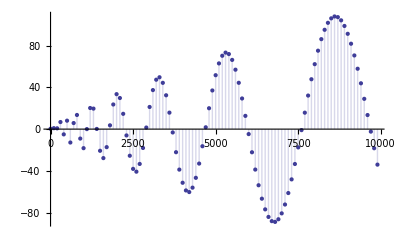

```mathematica
DiscretePlot[ Re@Zeta[.2+13I,n],{n,1,10000,100}]
```

```mathematica
ps[n_,s_]:= (s-1)(Zeta[s]-HarmonicNumber[n,s])+s n^(1-2s)( Zeta[1-s]-HarmonicNumber[n,1-s])
ps2[n_,s_]:= (Zeta[s]-HarmonicNumber[n,s])+(s/(s-1)) n^(1-2s)( Zeta[1-s]-HarmonicNumber[n,1-s])
ps3[n_,s_]:= (2^s Pi^(s-1) Sin[ Pi s / 2] Gamma[1-s] Zeta[1-s]-HarmonicNumber[n,s])+(s/(s-1)) n^(1-2s)( Zeta[1-s]-HarmonicNumber[n,1-s])
ps4[n_,s_]:= (2^s Pi^(s-1) Sin[ Pi s / 2] Gamma[1-s]) Zeta[1-s]-HarmonicNumber[n,s]+(s/(s-1)) n^(1-2s) Zeta[1-s]-(s/(s-1)) n^(1-2s)HarmonicNumber[n,1-s]
ps5[n_,s_]:= ((2^s Pi^(s-1) Sin[ Pi s / 2] Gamma[1-s])+(s/(s-1)) n^(1-2s)) Zeta[1-s]-(HarmonicNumber[n,s]+(s/(s-1)) n^(1-2s)HarmonicNumber[n,1-s])
ps6[n_,s_]:= (HarmonicNumber[n,s]+(s/(s-1)) n^(1-2s)HarmonicNumber[n,1-s])/((2^s Pi^(s-1) Sin[ Pi s / 2] Gamma[1-s])+(s/(s-1)) n^(1-2s)) 
ps7[n_,s_]:=(HarmonicNumber[n,1-s]-(n^(1-2 (1-s)) (1-s) HarmonicNumber[n,s])/s)/(-(n^(1-2 (1-s)) (1-s))/s+2^(1-s) π^-s Gamma[s] Sin[1/2 π (1-s)])
ps8[n_,s_]:=((2 π)^s (n s HarmonicNumber[n,1-s]+n^(2 s) (-1+s) HarmonicNumber[n,s]))/(n^(2 s) (2 π)^s (-1+s)+2 n s Cos[(π s)/2] Gamma[s])
ps8a[n_,s_]:=(2 π)^s (n s HarmonicNumber[n,1-s]+n^(2 s) (-1+s) HarmonicNumber[n,s])(n^(2 s) (2 π)^s (-1+s)+2 n s Cos[(π s)/2] Gamma[s])^-1
ps8b[n_,s_]:=(2 π)^s (n s HarmonicNumber[n,1-s]+n^(2 s) (-1+s) HarmonicNumber[n,s])(n^(2 s) (2 π)^s (-1+s)+2 n s Cos[(π s)/2] Gamma[s])^-1
ps8c[n_,s_]:={(n (2 π)^s s HarmonicNumber[n,1-s])/(n^(2 s) (2 π)^s (-1+s)+2 n s Cos[(π s)/2] Gamma[s]),-(n^(2 s) (2 π)^s HarmonicNumber[n,s])/(n^(2 s) (2 π)^s (-1+s)+2 n s Cos[(π s)/2] Gamma[s]),+(n^(2 s) (2 π)^s s HarmonicNumber[n,s])/(n^(2 s) (2 π)^s (-1+s)+2 n s Cos[(π s)/2] Gamma[s])}
ps9[n_,s_]:=(2 π)^s (n s HarmonicNumber[n,1-s]+n^(2 s) (-1+s) HarmonicNumber[n,s])(n^(2 s) (2 π)^s (-1+s)+2 n s Cos[(π s)/2] Gamma[s])^-1
ps10[n_,s_]:= (n s HarmonicNumber[n,1-s]-n^(2 s) (1-s) HarmonicNumber[n,s])(n^(2 s)  (-1+s)+2 n s(2 π)^-s Cos[(π s)/2] Gamma[s])^-1
ps11[n_,s_]:= (n^(1-s) s HarmonicNumber[n,1-s]-n^s (1-s) HarmonicNumber[n,s])(2 n^(1-s) s(2 π)^-s Cos[(π s)/2] Gamma[s]-n^s  (1-s))^-1
ps11a[n_,s_]:= (n^(1-s) s HarmonicNumber[n,1-s]-n^s (1-s) HarmonicNumber[n,s])/(2^(1-s) n^(1-s) s π^-s Cos[(π s)/2] Gamma[s]-n^s  (1-s))
ps11b[n_,s_]:=(-n^(1/2-ⅈ s) (1/2+ⅈ s) HarmonicNumber[n,1/2-ⅈ s]+n^(1/2+ⅈ s) (1/2-ⅈ s) HarmonicNumber[n,1/2+ⅈ s])/(-n^(1/2-ⅈ s) (1/2+ⅈ s)+2^(1/2+ⅈ s) n^(1/2+ⅈ s) π^(-1/2+ⅈ s) (1/2-ⅈ s) Cos[1/2 π (1/2-ⅈ s)] Gamma[1/2-ⅈ s])
ps11c[n_,s_]:=ps11b[n,s I-I/2]
ps12[n_,s_]:= (n^(1-s) s HarmonicNumber[n,1-s])(2 n^(1-s) s(2 π)^-s Cos[(π s)/2] Gamma[s]-n^s  (1-s))^-1 - (n^s (1-s) HarmonicNumber[n,s])(2 n^(1-s) s(2 π)^-s Cos[(π s)/2] Gamma[s]-n^s  (1-s))^-1
ps13[n_,s_]:=  HarmonicNumber[n,1-s]/(2 (2 π)^-s Cos[(π s)/2] Gamma[s]-n^(2s-1)  (1-s)/s) - (n^s (1-s) HarmonicNumber[n,s])/(2 n^(1-s) s(2 π)^-s Cos[(π s)/2] Gamma[s]-n^s  (1-s))
ps14[n_,s_]:=   HarmonicNumber[n,s](1-2 n^(1-2s) (s/(1-s))(2 π)^-s Cos[(π s)/2] Gamma[s])^-1-HarmonicNumber[n,1-s](n^(2s-1)  (1-s)/s-2 (2 π)^-s Cos[(π s)/2] Gamma[s])^-1
```

```mathematica
ps11a[100000000000,(.65+I)]
```

0.243869-0.814324 ⅈ

```mathematica
N@Zeta[.65+I]
```

0.243869-0.814324 ⅈ

```mathematica
FullSimplify@ps6[n,1-s]
```

((2 π)^s (n s HarmonicNumber[n,1-s]+n^(2 s) (-1+s) HarmonicNumber[n,s]))/(n^(2 s) (2 π)^s (-1+s)+2 n s Cos[(π s)/2] Gamma[s])

```mathematica
N@ps8c[100000000000000000,N@ZetaZero@1]
```

{-2.07228×10^7-3.29905×10^6 ⅈ,-181312.+1.47251×10^6 ⅈ,2.09042×10^7+1.82654×10^6 ⅈ}

```mathematica
Expand[((2 π)^s (n s HarmonicNumber[n,1-s]+n^(2 s) (-1+s) HarmonicNumber[n,s]))/(n^(2 s) (2 π)^s (-1+s)+2 n s Cos[(π s)/2] Gamma[s])]
```

(n (2 π)^s s HarmonicNumber[n,1-s])/(n^(2 s) (2 π)^s (-1+s)+2 n s Cos[(π s)/2] Gamma[s])-(n^(2 s) (2 π)^s HarmonicNumber[n,s])/(n^(2 s) (2 π)^s (-1+s)+2 n s Cos[(π s)/2] Gamma[s])+(n^(2 s) (2 π)^s s HarmonicNumber[n,s])/(n^(2 s) (2 π)^s (-1+s)+2 n s Cos[(π s)/2] Gamma[s])

```mathematica
2^s Pi^(s-1) Sin[ Pi s / 2] Gamma[1-s] Zeta[1-s]/.s->1/2+s
```

2^(1/2+s) π^(-1/2+s) Gamma[1/2-s] Sin[1/2 π (1/2+s)] Zeta[1/2-s]

```mathematica
n^x / (n^(-x))
```

n^(2 x)

```mathematica
FullSimplify[(-1/2+x)/(-1/2-x)]/.x->s
```

-1+2/(1+2 s)

```mathematica
ps11b[100000,(.3+2I)I-I/2]
```

0.385062-0.282542 ⅈ

```mathematica
Zeta[.3+2 I]
```

0.38531-0.282528 ⅈ

```mathematica
Expand[(1/2-s)/I]
```

-ⅈ/2+ⅈ s

```mathematica
ts[n_,s_]:= (-1/2-s)n^(-s)(Zeta[1/2-s] - HarmonicNumber[n,1/2-s])-(-1/2+s)n^(s)(Zeta[1/2+s] - HarmonicNumber[n,1/2+s])
ts2[n_,s_]:=n^(-s)(Zeta[1/2-s] - HarmonicNumber[n,1/2-s])-(-1/2+s)n^(s)/(-1/2-s)(Zeta[1/2+s] - HarmonicNumber[n,1/2+s])
ts3[n_,s_]:=n^(-s)(Zeta[1/2-s] - HarmonicNumber[n,1/2-s])-(-1/2+s)n^(s)/(-1/2-s)(2^(1/2+s) π^(-1/2+s) Gamma[1/2-s] Sin[1/2 π (1/2+s)] Zeta[1/2-s] - HarmonicNumber[n,1/2+s])
ts4[n_,s_]:=n^-s Zeta[1/2-s] - n^-s HarmonicNumber[n,1/2-s]-(-1/2+s)n^(s)/(-1/2-s)(2^(1/2+s) π^(-1/2+s) Gamma[1/2-s] Sin[1/2 π (1/2+s)] Zeta[1/2-s] - HarmonicNumber[n,1/2+s])
ts5[n_,s_]:=n^-s Zeta[1/2-s] - n^-s HarmonicNumber[n,1/2-s]-(-1/2+s)n^(s)/(-1/2-s)2^(1/2+s) π^(-1/2+s) Gamma[1/2-s] Sin[1/2 π (1/2+s)] Zeta[1/2-s] +(-1/2+s)n^(s)/(-1/2-s) HarmonicNumber[n,1/2+s]
ts6[n_,s_]:=n^-s Zeta[1/2-s] -(-1/2+s)n^(s)/(-1/2-s)2^(1/2+s) π^(-1/2+s) Gamma[1/2-s] Sin[1/2 π (1/2+s)] Zeta[1/2-s] +(-1/2+s)n^(s)/(-1/2-s) HarmonicNumber[n,1/2+s]- n^-s HarmonicNumber[n,1/2-s]
ts7[n_,s_]:=(n^-s -(-1/2+s)n^(s)/(-1/2-s)2^(1/2+s) π^(-1/2+s) Gamma[1/2-s] Sin[1/2 π (1/2+s)]) Zeta[1/2-s] +(-1/2+s)n^s/(-1/2-s) HarmonicNumber[n,1/2+s]- n^-s HarmonicNumber[n,1/2-s]
ts8[n_,s_]:=(n^-s -(-1/2+s)n^(s)/(-1/2-s)2^(1/2+s) π^(-1/2+s) Gamma[1/2-s] Sin[1/2 π (1/2+s)]) Zeta[1/2-s] +(-1+2/(1+2 s))n^s HarmonicNumber[n,1/2+s]- n^-s HarmonicNumber[n,1/2-s]
(* So this is Zeta[1/2-s] *)
ts9[n_,s_]:= (-(-1+2/(1+2 s))n^s HarmonicNumber[n,1/2+s]+ n^-s HarmonicNumber[n,1/2-s])/(n^-s -(-1/2+s)n^(s)/(-1/2-s)2^(1/2+s) π^(-1/2+s) Gamma[1/2-s] Sin[1/2 π (1/2+s)])
zt[n_,s_]:=ts9[n,1/2-s]
ts10[n_,s_]:=(√π ((1+2 s) HarmonicNumber[n,1/2-s]+n^(2 s) (-1+2 s) HarmonicNumber[n,1/2+s]))/(√π (1+2 s)-n^(2 s) ((2 π)^s-2^(1+s) π^s s) Gamma[1/2-s] (Cos[(π s)/2]+Sin[(π s)/2]))
zt10[n_,s_]:=ts10[n,1/2-s]
```

```mathematica
N@ts9[10000000000000,3I+.1]
```

0.513629+0.0713081 ⅈ

```mathematica
N@Zeta[-1.2]
```

-0.0547884

```mathematica
zt[10000000000,-1.2]
```

-0.0547884

```mathematica
FullSimplify@Expand[ (-(-1+2/(1+2 s))n^s HarmonicNumber[n,1/2+s]+ n^-s HarmonicNumber[n,1/2-s])/(n^-s -(-1/2+s)n^(s)/(-1/2-s)2^(1/2+s) π^(-1/2+s) Gamma[1/2-s] Sin[1/2 π (1/2+s)])]
```

(√π ((1+2 s) HarmonicNumber[n,1/2-s]+n^(2 s) (-1+2 s) HarmonicNumber[n,1/2+s]))/(√π (1+2 s)-n^(2 s) ((2 π)^s-2^(1+s) π^s s) Gamma[1/2-s] (Cos[(π s)/2]+Sin[(π s)/2]))

```mathematica
zt10[10000000000,N@ZetaZero@1]
```

-8.96391×10^-7+5.63064×10^-6 ⅈ

```mathematica
qs[n_,s_]:= (-1/2+s)n^(s)(Zeta[1/2+s] - HarmonicNumber[n,1/2+s])-(-1/2-s)n^(-s)(Zeta[1/2-s] - HarmonicNumber[n,1/2-s])
qs2[n_,s_]:= (-1/2+s)n^(s)((2^(1/2+s) π^(-1/2+s) Gamma[1/2-s] Sin[1/2 π (1/2+s)] Zeta[1/2-s]) - HarmonicNumber[n,1/2+s])-(-1/2-s)n^(-s)(Zeta[1/2-s] - HarmonicNumber[n,1/2-s])
qs3[n_,s_]:= n^s(2^(1/2+s) π^(-1/2+s) Gamma[1/2-s] Sin[1/2 π (1/2+s)] Zeta[1/2-s]) -n^s HarmonicNumber[n,1/2+s]-((1+2 s)/(1-2 s))n^-s Zeta[1/2-s] + ((1+2 s)/(1-2 s))n^-s HarmonicNumber[n,1/2-s]
qs4[n_,s_]:= (n^s(2^(1/2+s) π^(-1/2+s) Gamma[1/2-s] Sin[1/2 π (1/2+s)] ) -((1+2 s)/(1-2 s))n^-s )Zeta[1/2-s] + ((1+2 s)/(1-2 s))n^-s HarmonicNumber[n,1/2-s]-n^s HarmonicNumber[n,1/2+s]
qs5[n_,s_]:=  (n^s HarmonicNumber[n,1/2+s]-((1+2 s)/(1-2 s))n^-s HarmonicNumber[n,1/2-s])/((n^s(2^(1/2+s) π^(-1/2+s) Gamma[1/2-s] Sin[1/2 π (1/2+s)] ) -((1+2 s)/(1-2 s))n^-s ))
qt[n_,s_]:=qs5[n,1/2-s]
qs6[n_,s_]:=((1+2 s) HarmonicNumber[n,1/2-s]+n^(2 s) (-1+2 s) HarmonicNumber[n,1/2+s])/(1+2 s-2^s n^(2 s) π^(-1/2+s) (1-2 s) Gamma[1/2-s] (Cos[(π s)/2]+Sin[(π s)/2]))
qt6[n_,s_]:=qs6[n,1/2-s]
qs7[n_,s_]:=(HarmonicNumber[n,1/2-s]+n^(2 s) (-1+2 s)/(1+2 s) HarmonicNumber[n,1/2+s])/(1-2^s n^(2 s) π^(-1/2+s) (1-2 s)/(1+2 s) Gamma[1/2-s] (Cos[(π s)/2]+Sin[(π s)/2]))
qt7[n_,s_]:=qs7[n,1/2-s]
qs8[n_,s_]:=(n^-s HarmonicNumber[n,1/2-s]+n^s (-1+2 s)/(1+2 s) HarmonicNumber[n,1/2+s])/(n^-s -2^s n^s π^(-1/2+s) (1-2 s)/(1+2 s) Gamma[1/2-s] (Cos[(π s)/2]+Sin[(π s)/2]))
qt8[n_,s_]:=qs8[n,1/2-s]
```

```mathematica
N@qt8[10000,3I+.1]
```

0.457347-0.0455962 ⅈ

```mathematica
Zeta[3I + .1]
```

0.457485-0.0457237 ⅈ

```mathematica
FullSimplify[(n^s HarmonicNumber[n,1/2+s]-((1+2 s)/(1-2 s))n^-s HarmonicNumber[n,1/2-s])/((n^s(2^(1/2+s) π^(-1/2+s) Gamma[1/2-s] Sin[1/2 π (1/2+s)] ) -((1+2 s)/(1-2 s))n^-s ))]
```

(√π ((1+2 s) HarmonicNumber[n,1/2-s]+n^(2 s) (-1+2 s) HarmonicNumber[n,1/2+s]))/(√π (1+2 s)-n^(2 s) ((2 π)^s-2^(1+s) π^s s) Gamma[1/2-s] (Cos[(π s)/2]+Sin[(π s)/2]))

```mathematica
FullSimplify[((2 π)^s-2^(1+s) π^s s) / (Pi^(1/2))]
```

2^s π^(-1/2+s) (1-2 s)

```mathematica
((1+2 s) HarmonicNumber[n,1/2-s]+n^(2 s) (-1+2 s) HarmonicNumber[n,1/2+s])/((1+2 s)-n^(2 s) 2^s π^(-1/2+s) (1-2 s) Gamma[1/2-s] (Cos[(π s)/2]+Sin[(π s)/2]))
```

((1+2 s) HarmonicNumber[n,1/2-s]+n^(2 s) (-1+2 s) HarmonicNumber[n,1/2+s])/(1+2 s-2^s n^(2 s) π^(-1/2+s) (1-2 s) Gamma[1/2-s] (Cos[(π s)/2]+Sin[(π s)/2]))

```mathematica
FullSimplify[2^s n^(2 s) π^(-1/2+s) (1-2 s) Gamma[1/2-s] (Cos[(π s)/2]+Sin[(π s)/2])]
```

2^(1+s) n^(2 s) π^(-1/2+s) Gamma[3/2-s] (Cos[(π s)/2]+Sin[(π s)/2])

```mathematica
FullSimplify[(1-2 s)/(1+2s)]
```

-1+2/(1+2 s)

```mathematica
2^s n^(2 s) π^(-1/2+s) (-1+2/(1+2 s)) Gamma[1/2-s] (Cos[(π s)/2]+Sin[(π s)/2])
```

2^s n^(2 s) π^(-1/2+s) (-1+2/(1+2 s)) Gamma[1/2-s] (Cos[(π s)/2]+Sin[(π s)/2])

```mathematica
(n^(1-s) s HarmonicNumber[n,1-s]-n^s (1-s) HarmonicNumber[n,s])(2 n^(1-s) s(2 π)^-s Cos[(π s)/2] Gamma[s]-n^s  (1-s))^-1
```

(n^(1-s) s HarmonicNumber[n,1-s]-n^s (1-s) HarmonicNumber[n,s])/(-n^s (1-s)+2^(1-s) n^(1-s) π^-s s Cos[(π s)/2] Gamma[s])

```mathematica
(n^(1-s) s HarmonicNumber[n,1-s])(2 n^(1-s) s(2 π)^-s Cos[(π s)/2] Gamma[s]-n^s  (1-s))^-1
```

(n^(1-s) s HarmonicNumber[n,1-s])/(-n^s (1-s)+2^(1-s) n^(1-s) π^-s s Cos[(π s)/2] Gamma[s])

```mathematica
(n^(1-s) s HarmonicNumber[n,1-s])(2 n^(1-s) s(2 π)^-s Cos[(π s)/2] Gamma[s]-n^s  (1-s))^-1
```

(n^(1-s) s HarmonicNumber[n,1-s])/(-n^s (1-s)+2^(1-s) n^(1-s) π^-s s Cos[(π s)/2] Gamma[s])

```mathematica
xi[s_]:= 1/2 s (s-1) Pi^(-s/2) Gamma[ s/2] Zeta[s]
```

```mathematica
Limit[xi[s],s->ZetaZero[1]]
```

0

```mathematica
ps11[n_,s_]:= (n^(1-s) s HarmonicNumber[n,1-s]-n^s (1-s) HarmonicNumber[n,s])(2 n^(1-s) s(2 π)^-s Cos[(π s)/2] Gamma[s]-n^s  (1-s))^-1
```

```mathematica
Expand@ps11[n,s]
```

(n^(1-s) s HarmonicNumber[n,1-s])/(-n^s (1-s)+2^(1-s) n^(1-s) π^-s s Cos[(π s)/2] Gamma[s])-(n^s HarmonicNumber[n,s])/(-n^s (1-s)+2^(1-s) n^(1-s) π^-s s Cos[(π s)/2] Gamma[s])+(n^s s HarmonicNumber[n,s])/(-n^s (1-s)+2^(1-s) n^(1-s) π^-s s Cos[(π s)/2] Gamma[s])

```mathematica
ps14[n_,s_]:=   (1-2^(1-s) n^(1-2s) (s/(1-s))π^-s Cos[(π s)/2] Gamma[s])^-1 HarmonicNumber[n,s] -(n^(2s-1)  (1-s)/s-2^(1-s) π^-s Cos[(π s)/2] Gamma[s])^-1 HarmonicNumber[n,1-s]
ps14a[n_,s_]:=   {(1-2^(1-s) n^(1-2s) (s/(1-s))π^-s Cos[(π s)/2] Gamma[s])^-1, HarmonicNumber[n,s], -(n^(2s-1)  (1-s)/s-2^(1-s) π^-s Cos[(π s)/2] Gamma[s])^-1 ,HarmonicNumber[n,1-s]}
```

```mathematica
N@ps14a[100000000000,2.0]
```

{1.,1.64493,2.×10^-33,5.×10^21}

```mathematica
Cos[Pi .5 /2]
```

0.707107

```mathematica
Expand[(1-2 n^(1-2s) (s/(1-s))(2 π)^-s Cos[(π s)/2] Gamma[s])^-1]/.s->.5
```

-4.5036×10^15

```mathematica
ps14[100000,2.0]
```

1.64493

```mathematica
Zeta[.3]
```

-0.904559

```mathematica
(n^(2s-1)  (1-s)/s-2 (2 π)^-s Cos[(π s)/2] Gamma[s])^-1
```

1/((n^(-1+2 s) (1-s))/s-2^(1-s) π^-s Cos[(π s)/2] Gamma[s])

```mathematica
ps15[n_,s_]:=  Sum[ ((1-2^(1-s) n^(1-2s) (s/(1-s))π^-s Cos[(π s)/2] Gamma[s])^-1) j^-s -((n^(2s-1)  (1-s)/s-2^(1-s) π^-s Cos[(π s)/2] Gamma[s])^-1) j^(s-1),{j,1,n}]
```

```mathematica
ps15[10000,.5+I]
```

0.14191-0.711931 ⅈ

```mathematica
Zeta[.5+I]
```

0.143936-0.7221 ⅈ

```mathematica
((1-2^(1-s) n^(1-2s) (s/(1-s))π^-s Cos[(π s)/2] Gamma[s])^-1) j^-s -((n^(2s-1)  (1-s)/s-2^(1-s) π^-s Cos[(π s)/2] Gamma[s])^-1) j^(s-1)
```

-j^(-1+s)/((n^(-1+2 s) (1-s))/s-2^(1-s) π^-s Cos[(π s)/2] Gamma[s])+j^-s/(1-(2^(1-s) n^(1-2 s) π^-s s Cos[(π s)/2] Gamma[s])/(1-s))

```mathematica
ps11[n_,s_]:= (n^(1-s) s HarmonicNumber[n,1-s]-n^s (1-s) HarmonicNumber[n,s])(2 n^(1-s) s(2 π)^-s Cos[(π s)/2] Gamma[s]-n^s  (1-s))^-1
ps11a[n_,s_]:= Sum[(n^(1-s) s j^(s-1)-n^s (1-s) j^-s)(2 n^(1-s) s(2 π)^-s Cos[(π s)/2] Gamma[s]-n^s  (1-s))^-1,{j,1,n}]
```

```mathematica
ps11a[10000,.5+I]
```

0.14191-0.711931 ⅈ

```mathematica
qs9[n_,s_]:=((1+2 s)n^-s  HarmonicNumber[n,1/2-s]+n^s (-1+2 s) HarmonicNumber[n,1/2+s])/((1+2 s)n^-s -2^s n^s π^(-1/2+s) (1-2 s) Gamma[1/2-s] (Cos[(π s)/2]+Sin[(π s)/2]))
qt9[n_,s_]:=qs9[n,1/2-s]
qs9a[n_,s_]:=Sum[((1+2 s)n^-s  j^(-1/2+s)+n^s (-1+2 s) j^(-1/2-s))/((1+2 s)n^-s -2^s n^s π^(-1/2+s) (1-2 s) Gamma[1/2-s] (Cos[(π s)/2]+Sin[(π s)/2])),{j,1,n}]
qt9a[n_,s_]:=qs9a[n,1/2-s]
qs9b[n_,s_]:=Sum[1/j^(1/2)((1+2 s)( j/n)^s+(-1+2 s) (j/n)^-s)/((1+2 s)n^-s -2^s n^s π^(-1/2+s) (1-2 s) Gamma[1/2-s] (Cos[(π s)/2]+Sin[(π s)/2])),{j,1,n}]
qt9b[n_,s_]:=qs9b[n,1/2-s]
qs9c[n_,s_]:=Sum[1/j^(1/2)(2s(( j/n)^s+(j/n)^-s)+(( j/n)^s-(j/n)^-s))/((1+2 s)n^-s -2^s n^s π^(-1/2+s) (1-2 s) Gamma[1/2-s] (Cos[(π s)/2]+Sin[(π s)/2])),{j,1,n}]
qt9c[n_,s_]:=qs9c[n,1/2-s]
qs9d[n_,s_]:=Sum[1/j^(1/2)(4s Cosh[s Log[j/n]]+2Sinh[s Log[j/n]])/((1+2 s)n^-s -2^s n^s π^(-1/2+s) (1-2 s) Gamma[1/2-s] (Cos[(π s)/2]+Sin[(π s)/2])),{j,1,n}]
qt9d[n_,s_]:=qs9d[n,1/2-s]
```

```mathematica
qt9d[10000,-.5]
```

-0.207886

```mathematica
qs9ca[n_,s_]:=Sum[1/j^(1/2)(2s(( j/n)^s+(j/n)^-s)+(( j/n)^s-(j/n)^-s))/((1+2 s)E^(-s Log[n]) -(1-2 s)E^(s Log[2]) E^(s Log[n]) E^((-1/2+s)Log[π])  Gamma[1/2-s] (1/2(E^((π s)/2 I)+E^(-(π s)/2 I))+1/(2I)(E^((π s)/2 I)-E^(-(π s)/2 I)))),{j,1,n}]
qt9ca[n_,s_]:=qs9ca[n,1/2-s]
qs9cb[n_,s_]:=Sum[1/j^(1/2)(2s(( j/n)^s+(j/n)^-s)+(( j/n)^s-(j/n)^-s))/((1+2 s)E^(-s Log[n]) -(1-2 s) E^(s Log[n])E^(s Log[2]) E^((-1/2+s)Log[π])  Gamma[1/2-s] (1/2(E^((π s)/2 I)+E^(-(π s)/2 I))+1/(2I)(E^((π s)/2 I)-E^(-(π s)/2 I)))),{j,1,n}]
qt9cb[n_,s_]:=qs9cb[n,1/2-s]
qs9cc[n_,s_]:=Sum[1/j^(1/2)(2s(( j/n)^s+(j/n)^-s)+(( j/n)^s-(j/n)^-s))/((1+2 s)E^(-s Log[n]) -(1-2 s) E^(s Log[n])E^(s Log[2]) E^((-1/2+s)Log[π])  Gamma[1/2-s] (1/2(E^((π s)/2 I)+E^(-(π s)/2 I))+1/(2I)(E^((π s)/2 I)-E^(-(π s)/2 I)))),{j,1,n}]
qt9cc[n_,s_]:=qs9cc[n,1/2-s]
```

```mathematica
qt9cc[10000,-.5]
```

-0.207886+0. ⅈ

```mathematica
Expand[(1+2 s)E^(-s Log[n]) -(1-2 s) E^(s Log[n])E^(s Log[2]) E^((-1/2+s)Log[π])  Gamma[1/2-s] (1/2(E^((π s)/2 I)+E^(-(π s)/2 I))+1/(2I)(E^((π s)/2 I)-E^(-(π s)/2 I)))]
```

n^-s+2 n^-s s-(1+ⅈ) 2^(-1+s) ⅇ^(-1/2 ⅈ π s) n^s π^(-1/2+s) Gamma[1/2-s]-(1-ⅈ) 2^(-1+s) ⅇ^((ⅈ π s)/2) n^s π^(-1/2+s) Gamma[1/2-s]+(1+ⅈ) 2^s ⅇ^(-1/2 ⅈ π s) n^s π^(-1/2+s) s Gamma[1/2-s]+(1-ⅈ) 2^s ⅇ^((ⅈ π s)/2) n^s π^(-1/2+s) s Gamma[1/2-s]

```mathematica
ps11[n_,s_]:= (n^(1-s) s HarmonicNumber[n,1-s]-n^s (1-s) HarmonicNumber[n,s])/(2^(1-s) n^(1-s) s π^-s Cos[(π s)/2] Gamma[s]-n^s  (1-s))
ps14[n_,s_]:=   HarmonicNumber[n,s](1-2 n^(1-2s) (s/(1-s))(2 π)^-s Cos[(π s)/2] Gamma[s])^-1-HarmonicNumber[n,1-s](n^(2s-1)  (1-s)/s-2 (2 π)^-s Cos[(π s)/2] Gamma[s])^-1
ps14a1[n_,s_]:=   HarmonicNumber[n,s](1-2 n^(1-2s) (s/(1-s))(2 π)^-s Cos[(π s)/2] Gamma[s])^-1
ps14a2[n_,s_]:=   HarmonicNumber[n,1-s](n^(2s-1)  (1-s)/s-2 (2 π)^-s Cos[(π s)/2] Gamma[s])^-1
```

```mathematica
ps14[n,1-s]
```

HarmonicNumber[n,1-s]/(1-(2^s n^(1-2 (1-s)) π^(-1+s) (1-s) Cos[1/2 π (1-s)] Gamma[1-s])/s)-HarmonicNumber[n,s]/((n^(-1+2 (1-s)) s)/(1-s)-2^s π^(-1+s) Cos[1/2 π (1-s)] Gamma[1-s])

```mathematica
Expand[1-2(1-s)]
```

-1+2 s

```mathematica
Expand[-1+2(1-s)]
```

1-2 s

```mathematica
FullSimplify[ps14[n,s]+ps14[n,1-s]]
```

((n s HarmonicNumber[n,1-s]+n^(2 s) (-1+s) HarmonicNumber[n,s]) (n π ((2 π)^s s+2 Cos[(π s)/2] Gamma[1+s])-n^(2 s) (2 π)^s (π-π s+(2 π)^s Gamma[2-s] Sin[(π s)/2])))/((n^(2 s) (2 π)^s (-1+s)+2 n s Cos[(π s)/2] Gamma[s]) (n π s-n^(2 s) (2 π)^s Gamma[2-s] Sin[(π s)/2]))

```mathematica
ps14[n,s]-ps14[n,1-s]
```

-HarmonicNumber[n,1-s]/(1-(2^s n^(1-2 (1-s)) π^(-1+s) (1-s) Cos[1/2 π (1-s)] Gamma[1-s])/s)-HarmonicNumber[n,1-s]/((n^(-1+2 s) (1-s))/s-2^(1-s) π^-s Cos[(π s)/2] Gamma[s])+HarmonicNumber[n,s]/((n^(-1+2 (1-s)) s)/(1-s)-2^s π^(-1+s) Cos[1/2 π (1-s)] Gamma[1-s])+HarmonicNumber[n,s]/(1-(2^(1-s) n^(1-2 s) π^-s s Cos[(π s)/2] Gamma[s])/(1-s))

```mathematica
ps14[n,s]ps14[n,1-s]
```

(HarmonicNumber[n,1-s]/(1-(2^s n^(1-2 (1-s)) π^(-1+s) (1-s) Cos[1/2 π (1-s)] Gamma[1-s])/s)-HarmonicNumber[n,s]/((n^(-1+2 (1-s)) s)/(1-s)-2^s π^(-1+s) Cos[1/2 π (1-s)] Gamma[1-s])) (-HarmonicNumber[n,1-s]/((n^(-1+2 s) (1-s))/s-2^(1-s) π^-s Cos[(π s)/2] Gamma[s])+HarmonicNumber[n,s]/(1-(2^(1-s) n^(1-2 s) π^-s s Cos[(π s)/2] Gamma[s])/(1-s)))

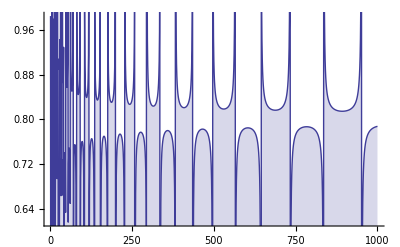

```mathematica
DiscretePlot[{Re@ps14[n,.5+24.14I]},{n,1,1000}]
```

```mathematica
Zeta[.8+1.14I]
```

0.419338-0.765218 ⅈ

```mathematica
D[ps14[n,s],n]
```

(n^(-2+2 s) (1-s) (-1+2 s) HarmonicNumber[n,1-s])/(s ((n^(-1+2 s) (1-s))/s-2^(1-s) π^-s Cos[(π s)/2] Gamma[s])^2)+(2^(1-s) n^(-2 s) π^-s (1-2 s) s Cos[(π s)/2] Gamma[s] HarmonicNumber[n,s])/((1-s) (1-(2^(1-s) n^(1-2 s) π^-s s Cos[(π s)/2] Gamma[s])/(1-s))^2)-((1-s) (-HarmonicNumber[n,2-s]+Zeta[2-s]))/((n^(-1+2 s) (1-s))/s-2^(1-s) π^-s Cos[(π s)/2] Gamma[s])+(s (-HarmonicNumber[n,1+s]+Zeta[1+s]))/(1-(2^(1-s) n^(1-2 s) π^-s s Cos[(π s)/2] Gamma[s])/(1-s))

```mathematica
px[n_,s_]:=1-2 n^(1-2s) (s/(1-s))(2 π)^-s Cos[(π s)/2] Gamma[s]
px2[n_,s_]:=n^(2s-1)  (1-s)/s-2 (2 π)^-s Cos[(π s)/2] Gamma[s]
```

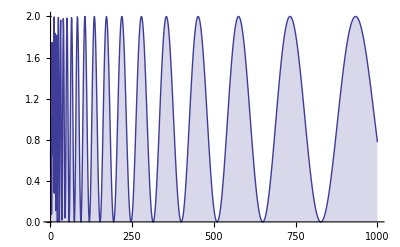

```mathematica
DiscretePlot[Re@px[n,.5+13I],{n,1,1000}]
```

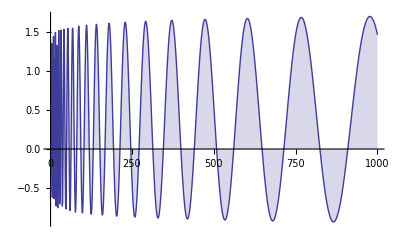

```mathematica
DiscretePlot[Re@px2[n,.52+13I],{n,1,1000}]
```

```mathematica
ps20[n_,s_]:=   HarmonicNumber[n,s]1/2 s (s-1)Pi^(-s/2)Gamma[s/2]/(1-2 n^(1-2s) (s/(1-s))(2 π)^-s Cos[(π s)/2] Gamma[s])-HarmonicNumber[n,1-s]1/2 s (s-1)Pi^(-s/2)Gamma[s/2]/(n^(2s-1)  (1-s)/s-2 (2 π)^-s Cos[(π s)/2] Gamma[s])
ps21[n_,s_]:=   HarmonicNumber[n,s]1/2 Pi^(-s/2)Gamma[s/2]/(1/(s(s-1))+2 n^(1-2s) (1/(1-s))(2 π)^-s Cos[(π s)/2] Gamma[s])-HarmonicNumber[n,1-s]1/2 s (s-1)Pi^(-s/2)Gamma[s/2]/(n^(2s-1)  (1-s)/s-2 (2 π)^-s Cos[(π s)/2] Gamma[s])
xi[s_]:= 1/2 s (s-1)Pi^(-s/2)Gamma[s/2]Zeta[s]
```

```mathematica
N@xi[2]
```

0.523599

```mathematica
ps21[10000000,2.0]
```

0.523599

```mathematica
ps30[n_,s_]:=   HarmonicNumber[n,s](1-2 n^(1-2s) (s/(1-s))(2 π)^-s Cos[(π s)/2] Gamma[s])^-1-HarmonicNumber[n,1-s](n^(2s-1)  (1-s)/s-2 (2 π)^-s Cos[(π s)/2] Gamma[s])^-1
ps31[n_,s_]:=   HarmonicNumber[n,1-s]/(1-(2^s n^(1-2 (1-s)) π^(-1+s) (1-s) Cos[1/2 π (1-s)] Gamma[1-s])/s)-HarmonicNumber[n,s]/((n^(-1+2 (1-s)) s)/(1-s)-2^s π^(-1+s) Cos[1/2 π (1-s)] Gamma[1-s])
ps32[n_,s_]:=-HarmonicNumber[n,1-s]/((n^(-1+2 s) (1-s))/s-2^(1-s) π^-s Cos[(π s)/2] Gamma[s])+HarmonicNumber[n,s]/(1-(2^(1-s) n^(1-2 s) π^-s s Cos[(π s)/2] Gamma[s])/(1-s))
ps33[n_,s_]:=(1/(1-(2^s n^(1-2 (1-s)) π^(-1+s) (1-s) Cos[1/2 π (1-s)] Gamma[1-s])/s)-1/((n^(-1+2 s) (1-s))/s-2^(1-s) π^-s Cos[(π s)/2] Gamma[s]))HarmonicNumber[n,1-s]+(1/(1-(2^(1-s) n^(1-2 s) π^-s s Cos[(π s)/2] Gamma[s])/(1-s))-1/((n^(-1+2 (1-s)) s)/(1-s)-2^s π^(-1+s) Cos[1/2 π (1-s)] Gamma[1-s]))HarmonicNumber[n,s]
ps33a[n_,s_]:={(1/(1-(2^s n^(1-2 (1-s)) π^(-1+s) (1-s) Cos[1/2 π (1-s)] Gamma[1-s])/s)-1/((n^(-1+2 s) (1-s))/s-2^(1-s) π^-s Cos[(π s)/2] Gamma[s])),HarmonicNumber[n,1-s],(1/(1-(2^(1-s) n^(1-2 s) π^-s s Cos[(π s)/2] Gamma[s])/(1-s))-1/((n^(-1+2 (1-s)) s)/(1-s)-2^s π^(-1+s) Cos[1/2 π (1-s)] Gamma[1-s])),HarmonicNumber[n,s]}
ps33b[n_,s_]:={(1/(1-(2^s n^(1-2 (1-s)) π^(-1+s) (1-s) Cos[1/2 π (1-s)] Gamma[1-s])/s)-1/((n^(-1+2 s) (1-s))/s-2^(1-s) π^-s Cos[(π s)/2] Gamma[s]))HarmonicNumber[n,1-s],(1/(1-(2^(1-s) n^(1-2 s) π^-s s Cos[(π s)/2] Gamma[s])/(1-s))-1/((n^(-1+2 (1-s)) s)/(1-s)-2^s π^(-1+s) Cos[1/2 π (1-s)] Gamma[1-s]))HarmonicNumber[n,s]}
ps35[n_,s_]:=(1/(1-(2^s n^(1-2 (1-s)) π^(-1+s) (1-s) Cos[1/2 π (1-s)] Gamma[1-s])/s)-1/((n^(-1+2 s) (1-s))/s-2^(1-s) π^-s Cos[(π s)/2] Gamma[s]))/(1/(1-(2^(1-s) n^(1-2 s) π^-s s Cos[(π s)/2] Gamma[s])/(1-s))-1/((n^(-1+2 (1-s)) s)/(1-s)-2^s π^(-1+s) Cos[1/2 π (1-s)] Gamma[1-s]))
ps36[n_,s_]:=(1/(1-(2^(1-s) n^(1-2 s) π^-s s Cos[(π s)/2] Gamma[s])/(1-s))-1/((n^(-1+2 (1-s)) s)/(1-s)-2^s π^(-1+s) Cos[1/2 π (1-s)] Gamma[1-s]))((n^(1-2 s) s)/(-1+s)HarmonicNumber[n,1-s]+HarmonicNumber[n,s])
ps37[n_,s_]:=(1/(1-(2^(1-s) n^(1-2 s) π^-s s Cos[(π s)/2] Gamma[s])/(1-s))-1/((n^(-1+2 (1-s)) s)/(1-s)-2^s π^(-1+s) Cos[1/2 π (1-s)] Gamma[1-s]))(1/(s-1)n^-s)(n^(1- s) sHarmonicNumber[n,1-s]+(s-1)n^s HarmonicNumber[n,s])
ps38[n_,s_]:=(-1/((1-s)-2^(1-s) n^(1-2 s) π^-s s Cos[(π s)/2] Gamma[s])+1/(n^(-1+2 (1-s)) s-(1-s)2^s π^(-1+s) Cos[1/2 π (1-s)] Gamma[1-s]))(n^-s)(n^(1- s) sHarmonicNumber[n,1-s]+(s-1)n^s HarmonicNumber[n,s])
ps39[n_,s_]:=(1/(s n^(1-s) -(1-s)n^s 2^s π^(-1+s) Cos[1/2 π (1-s)] Gamma[1-s])-1/((1-s)n^s-s n^(1- s)  2^(1-s) π^-s Cos[(π s)/2] Gamma[s]))(n^(1- s) sHarmonicNumber[n,1-s]-(1-s)n^s HarmonicNumber[n,s])
ps39a[n_,s_]:=n^(1- s) sHarmonicNumber[n,1-s]-(1-s)n^s HarmonicNumber[n,s]
ps39a2[n_,s_]:=Sum[ n^(1- s) s/j^(1-s)-(1-s)n^s /(j^s),{j,1,n}]
ps39b[n_,s_]:=(1/(s n^(1-s) -(1-s)n^s 2^s π^(-1+s) Cos[1/2 π (1-s)] Gamma[1-s])-1/((1-s)n^s-s n^(1- s)  2^(1-s) π^-s Cos[(π s)/2] Gamma[s]))
```

```mathematica
ps39[100000000,.3+13I]
```

0.880295-0.227194 ⅈ

```mathematica
Zeta[.3+13I]+Zeta[.7-13I]
```

0.880292-0.227193 ⅈ

```mathematica
ps39[100000000,.3+13I]
```

0.880295-0.227194 ⅈ

```mathematica
Zeta[.3+13I]-Zeta[.7-13I]
```

-0.129108-1.33067 ⅈ

```mathematica
ps32[1000000,.3+13I]-ps31[1000000,.3+13I]
```

-0.129069-1.33057 ⅈ

```mathematica
ps44[1000000,.3+13I]
```

-0.129069-1.33057 ⅈ

```mathematica
Chop@ps39a[1000,N@ZetaZero@5]
```

0.+32.9351 ⅈ

```mathematica
N@Im@ZetaZero@5
```

32.9351

```mathematica
Zeta[.3+13I]
```

0.375592-0.778932 ⅈ

```mathematica
FullSimplify[ps43a[n,s]]
```

(n^(-1+2 s) (-1+s))/s

```mathematica
ps40[n_,s_]:=(-HarmonicNumber[n,1-s]/((n^(-1+2 s) (1-s))/s-2^(1-s) π^-s Cos[(π s)/2] Gamma[s])+HarmonicNumber[n,s]/(1-(2^(1-s) n^(1-2 s) π^-s s Cos[(π s)/2] Gamma[s])/(1-s)))-( HarmonicNumber[n,1-s]/(1-(2^s n^(1-2 (1-s)) π^(-1+s) (1-s) Cos[1/2 π (1-s)] Gamma[1-s])/s)-HarmonicNumber[n,s]/((n^(-1+2 (1-s)) s)/(1-s)-2^s π^(-1+s) Cos[1/2 π (1-s)] Gamma[1-s]))
ps41[n_,s_]:=-HarmonicNumber[n,1-s]/((n^(-1+2 s) (1-s))/s-2^(1-s) π^-s Cos[(π s)/2] Gamma[s])+HarmonicNumber[n,s]/(1-(2^(1-s) n^(1-2 s) π^-s s Cos[(π s)/2] Gamma[s])/(1-s))- HarmonicNumber[n,1-s]/(1-(2^s n^(1-2 (1-s)) π^(-1+s) (1-s) Cos[1/2 π (1-s)] Gamma[1-s])/s)+HarmonicNumber[n,s]/((n^(-1+2 (1-s)) s)/(1-s)-2^s π^(-1+s) Cos[1/2 π (1-s)] Gamma[1-s])
ps42[n_,s_]:=(1/(1-(2^(1-s) n^(1-2 s) π^-s s Cos[(π s)/2] Gamma[s])/(1-s))+1/((n^(-1+2 (1-s)) s)/(1-s)-2^s π^(-1+s) Cos[1/2 π (1-s)] Gamma[1-s]))HarmonicNumber[n,s]-(1/((n^(-1+2 s) (1-s))/s-2^(1-s) π^-s Cos[(π s)/2] Gamma[s])+ 1/(1-(2^s n^(1-2 (1-s)) π^(-1+s) (1-s) Cos[1/2 π (1-s)] Gamma[1-s])/s))HarmonicNumber[n,1-s]
ps43[n_,s_]:=(1/(1-(2^(1-s) n^(1-2 s) π^-s s Cos[(π s)/2] Gamma[s])/(1-s))+1/((n^(-1+2 (1-s)) s)/(1-s)-2^s π^(-1+s) Cos[1/2 π (1-s)] Gamma[1-s]))HarmonicNumber[n,s]-(1/((n^(-1+2 s) (1-s))/s-2^(1-s) π^-s Cos[(π s)/2] Gamma[s])+ 1/(1-(2^s n^(1-2 (1-s)) π^(-1+s) (1-s) Cos[1/2 π (1-s)] Gamma[1-s])/s))HarmonicNumber[n,1-s]
ps43a[n_,s_]:=(1/(1-(2^(1-s) n^(1-2 s) π^-s s Cos[(π s)/2] Gamma[s])/(1-s))+1/((n^(-1+2 (1-s)) s)/(1-s)-2^s π^(-1+s) Cos[1/2 π (1-s)] Gamma[1-s]))/-(1/((n^(-1+2 s) (1-s))/s-2^(1-s) π^-s Cos[(π s)/2] Gamma[s])+ 1/(1-(2^s n^(1-2 (1-s)) π^(-1+s) (1-s) Cos[1/2 π (1-s)] Gamma[1-s])/s))
ps44[n_,s_]:=(1/((n^(-1+2 s) (1-s))/s-2^(1-s) π^-s Cos[(π s)/2] Gamma[s])+ 1/(1-(2^s n^(1-2 (1-s)) π^(-1+s) (1-s) Cos[1/2 π (1-s)] Gamma[1-s])/s))(1/s)(n^(-1+2s) (1-s)HarmonicNumber[n,s]-s  HarmonicNumber[n,1-s])
ps45[n_,s_]:=(1/((n^(-1+2 s) (1-s))/s-2^(1-s) π^-s Cos[(π s)/2] Gamma[s])+ 1/(1-(2^s n^(1-2 (1-s)) π^(-1+s) (1-s) Cos[1/2 π (1-s)] Gamma[1-s])/s))(1/s)n^s(n^(-1+s) (1-s)HarmonicNumber[n,s]-s n^-s HarmonicNumber[n,1-s])
ps46[n_,s_]:=(1/((1-s)n^(s-1) -s n^-s 2^(1-s) π^-s Cos[(π s)/2] Gamma[s])+ 1/(s n^-s -(1-s)n^(s-1)2^s  π^(-1+s)  Cos[1/2 π (1-s)] Gamma[1-s]))( (1-s)n^(s-1) HarmonicNumber[n,s]-s n^-s HarmonicNumber[n,1-s])
ps46a[n_,s_]:=( (1-s)n^(s-1) HarmonicNumber[n,s]-s n^-s HarmonicNumber[n,1-s])
```

```mathematica
Zeta[.4+17I]-Zeta[1-(.4+17I)]
```

0.157956+1.79925 ⅈ

```mathematica
ps46[1000000,.4+17I]
```

0.157881+1.79905 ⅈ

```mathematica
ps46a[1000,N@ZetaZero@5]*-1000
```

0.+32.9351 ⅈ

```mathematica
N@Im@ZetaZero@5
```

32.9351

```mathematica
FullSimplify[n^(1-2 (1-s)) n^-s]
```

n^(-1+s)

```mathematica
ps50[n_,s_]:=( HarmonicNumber[n,1-s]/(1-(2^s n^(1-2 (1-s)) π^(-1+s) (1-s) Cos[1/2 π (1-s)] Gamma[1-s])/s)-HarmonicNumber[n,s]/((n^(-1+2 (1-s)) s)/(1-s)-2^s π^(-1+s) Cos[1/2 π (1-s)] Gamma[1-s]))(-HarmonicNumber[n,1-s]/((n^(-1+2 s) (1-s))/s-2^(1-s) π^-s Cos[(π s)/2] Gamma[s])+HarmonicNumber[n,s]/(1-(2^(1-s) n^(1-2 s) π^-s s Cos[(π s)/2] Gamma[s])/(1-s)))
ps51[n_,s_]:=-HarmonicNumber[n,1-s]^2/((1-(2^s n^(1-2 (1-s)) π^(-1+s) (1-s) Cos[1/2 π (1-s)] Gamma[1-s])/s) ((n^(-1+2 s) (1-s))/s-2^(1-s) π^-s Cos[(π s)/2] Gamma[s]))+(2HarmonicNumber[n,1-s] HarmonicNumber[n,s])/(((n^(-1+2 (1-s)) s)/(1-s)-2^s π^(-1+s) Cos[1/2 π (1-s)] Gamma[1-s]) ((n^(-1+2 s) (1-s))/s-2^(1-s) π^-s Cos[(π s)/2] Gamma[s]))-HarmonicNumber[n,s]^2/(((n^(-1+2 (1-s)) s)/(1-s)-2^s π^(-1+s) Cos[1/2 π (1-s)] Gamma[1-s]) (1-(2^(1-s) n^(1-2 s) π^-s s Cos[(π s)/2] Gamma[s])/(1-s)))
ps52[n_,s_]:=(2HarmonicNumber[n,1-s] HarmonicNumber[n,s])/(((n^(-1+2 (1-s)) s)/(1-s)-2^s π^(-1+s) Cos[1/2 π (1-s)] Gamma[1-s]) ((n^(-1+2 s) (1-s))/s-2^(1-s) π^-s Cos[(π s)/2] Gamma[s]))-(HarmonicNumber[n,1-s]^2+(n^(-2+4 s) (-1+s)^2)/s^2 HarmonicNumber[n,s]^2)/((1-(2^s n^(1-2 (1-s)) π^(-1+s) (1-s) Cos[1/2 π (1-s)] Gamma[1-s])/s) ((n^(-1+2 s) (1-s))/s-2^(1-s) π^-s Cos[(π s)/2] Gamma[s]))
ps53[n_,s_]:=(2HarmonicNumber[n,1-s] HarmonicNumber[n,s])/(((n^(-1+2 (1-s)) s)/(1-s)-2^s π^(-1+s) Cos[1/2 π (1-s)] Gamma[1-s]) ((n^(-1+2 s) (1-s))/s-2^(1-s) π^-s Cos[(π s)/2] Gamma[s]))-(s^2 HarmonicNumber[n,1-s]^2+n^(-2+4 s) (-1+s)^2 HarmonicNumber[n,s]^2)/((s-2^s n^(1-2 (1-s)) π^(-1+s) (1-s) Cos[1/2 π (1-s)] Gamma[1-s]) (n^(-1+2 s) (1-s)-s 2^(1-s) π^-s Cos[(π s)/2] Gamma[s]))
ps54[n_,s_]:=(2HarmonicNumber[n,1-s] HarmonicNumber[n,s])/((n^(1-2s) s/(1-s)-2^s π^(-1+s) Cos[1/2 π (1-s)] Gamma[1-s]) (n^(-1+2 s)(1-s)/s-2^(1-s) π^-s Cos[(π s)/2] Gamma[s]))-(s^2 n^(-2s) HarmonicNumber[n,1-s]^2+n^(-2+2 s) (-1+s)^2 HarmonicNumber[n,s]^2)/((s n^-s -2^s n^(-1+s) π^(-1+s) (1-s) Cos[1/2 π (1-s)] Gamma[1-s]) (n^(-1+ s) (1-s)-s n^-s  2^(1-s) π^-s Cos[(π s)/2] Gamma[s]))
ps54a[n_,s_]:={1/((n^(1-2s) s/(1-s)-2^s π^(-1+s) Cos[1/2 π (1-s)] Gamma[1-s]) (n^(-1+2 s)(1-s)/s-2^(1-s) π^-s Cos[(π s)/2] Gamma[s])),2HarmonicNumber[n,1-s] HarmonicNumber[n,s],-1/((s n^-s -2^s n^(-1+s) π^(-1+s) (1-s) Cos[1/2 π (1-s)] Gamma[1-s]) (n^(-1+ s) (1-s)-s n^-s  2^(1-s) π^-s Cos[(π s)/2] Gamma[s])),s^2 n^(-2s) HarmonicNumber[n,1-s]^2+n^(-2+2 s) (-1+s)^2 HarmonicNumber[n,s]^2}
```

0.0263648+1.12757×10^-17 ⅈ

```mathematica
ps54[100000,.3+10I]
```

2.40802+0.0200895 ⅈ

```mathematica
Zeta[.3+10I]Zeta[1-(.3+10I)]
```

2.40847+0.0191575 ⅈ

```mathematica
Expand[( HarmonicNumber[n,1-s]/(1-(2^s n^(1-2 (1-s)) π^(-1+s) (1-s) Cos[1/2 π (1-s)] Gamma[1-s])/s)-HarmonicNumber[n,s]/((n^(-1+2 (1-s)) s)/(1-s)-2^s π^(-1+s) Cos[1/2 π (1-s)] Gamma[1-s]))(-HarmonicNumber[n,1-s]/((n^(-1+2 s) (1-s))/s-2^(1-s) π^-s Cos[(π s)/2] Gamma[s])+HarmonicNumber[n,s]/(1-(2^(1-s) n^(1-2 s) π^-s s Cos[(π s)/2] Gamma[s])/(1-s)))]
```

-HarmonicNumber[n,1-s]^2/((1-(2^s n^(1-2 (1-s)) π^(-1+s) (1-s) Cos[1/2 π (1-s)] Gamma[1-s])/s) ((n^(-1+2 s) (1-s))/s-2^(1-s) π^-s Cos[(π s)/2] Gamma[s]))+(HarmonicNumber[n,1-s] HarmonicNumber[n,s])/(((n^(-1+2 (1-s)) s)/(1-s)-2^s π^(-1+s) Cos[1/2 π (1-s)] Gamma[1-s]) ((n^(-1+2 s) (1-s))/s-2^(1-s) π^-s Cos[(π s)/2] Gamma[s]))+(HarmonicNumber[n,1-s] HarmonicNumber[n,s])/((1-(2^s n^(1-2 (1-s)) π^(-1+s) (1-s) Cos[1/2 π (1-s)] Gamma[1-s])/s) (1-(2^(1-s) n^(1-2 s) π^-s s Cos[(π s)/2] Gamma[s])/(1-s)))-HarmonicNumber[n,s]^2/(((n^(-1+2 (1-s)) s)/(1-s)-2^s π^(-1+s) Cos[1/2 π (1-s)] Gamma[1-s]) (1-(2^(1-s) n^(1-2 s) π^-s s Cos[(π s)/2] Gamma[s])/(1-s)))

```mathematica
FullSimplify[(((n^(-1+2 (1-s)) s)/(1-s)-2^s π^(-1+s) Cos[1/2 π (1-s)] Gamma[1-s]) ((n^(-1+2 s) (1-s))/s-2^(1-s) π^-s Cos[(π s)/2] Gamma[s]))/((1-(2^s n^(1-2 (1-s)) π^(-1+s) (1-s) Cos[1/2 π (1-s)] Gamma[1-s])/s) (1-(2^(1-s) n^(1-2 s) π^-s s Cos[(π s)/2] Gamma[s])/(1-s)))]
```

1

```mathematica
FullSimplify[((1-(2^s n^(1-2 (1-s)) π^(-1+s) (1-s) Cos[1/2 π (1-s)] Gamma[1-s])/s) ((n^(-1+2 s) (1-s))/s-2^(1-s) π^-s Cos[(π s)/2] Gamma[s]))/(((n^(-1+2 (1-s)) s)/(1-s)-2^s π^(-1+s) Cos[1/2 π (1-s)] Gamma[1-s]) (1-(2^(1-s) n^(1-2 s) π^-s s Cos[(π s)/2] Gamma[s])/(1-s)))]
```

```mathematica
FullSimplify[(n^(-2+4 s) (-1+s)^2)/s^2]
```

(n^(-2+4 s) (-1+s)^2)/s^2

```mathematica
FullSimplify[n^(1-2 (1-s)) n^-s]
```

n^(-1+s)

```mathematica
FullSimplify[n^(-1+2 (1-s))]
```

n^(1-2 s)

```mathematica
FullSimplify[(n^(1-2s) s/(1-s)-2^s π^(-1+s) Cos[1/2 π (1-s)] Gamma[1-s]) (n^(-1+2 s)(1-s)/s-2^(1-s) π^-s Cos[(π s)/2] Gamma[s])]
```

2-(2^s n^(-1+2 s) π^(-1+s) Gamma[2-s] Sin[(π s)/2])/s+(n^(1-2 s) (2 π)^-s Csc[(π s)/2] Gamma[1+s] Sin[π s])/(-1+s)

```mathematica
FullSimplify[Expand[(s n^-s -2^s n^(-1+s) π^(-1+s) (1-s) Cos[1/2 π (1-s)] Gamma[1-s]) (n^(-1+ s) (1-s)-s n^-s  2^(1-s) π^-s Cos[(π s)/2] Gamma[s])]]
```

2^-s n^(-2 (1+s)) π^(-1-s) (n^(2 s) (2 π)^s (-1+s)+2 n s Cos[(π s)/2] Gamma[s]) (-n π s+n^(2 s) (2 π)^s Gamma[2-s] Sin[(π s)/2])

```mathematica
ps54[100000000,N@ZetaZero@20]
```

2.56114×10^-9-1.45646×10^-12 ⅈ

```mathematica
ps54a[10000000000,.5+14I]
```

{0.365273+0. ⅈ,1.01913×10^8+0. ⅈ,-1.86126×10^7+5.7312×10^-10 ⅈ,2.00003+0. ⅈ}

```mathematica
HarmonicNumber[100,.5+I]HarmonicNumber[100,1-(.5+I)]
```

73.9495+0. ⅈ

```mathematica
n^(1/2+s I)n^(1/2-s I)
```

n

```mathematica
(1-(1/2+s I))
```

1/2-ⅈ s

```mathematica
Limit[s^2 n^(-2s) HarmonicNumber[n,1-s]^2+n^(-2+2 s) (-1+s)^2 HarmonicNumber[n,s]^2/.s->1/2+10I,n->Infinity]
```

2

```mathematica
Limit[s^2 n^(-2s) HarmonicNumber[n,1-s]^2+n^(-2+2 s) (-1+s)^2 HarmonicNumber[n,s]^2/.s->2/3+10I,n->Infinity]
```

2

```mathematica
ps54x[n_,s_]:=(2HarmonicNumber[n,1-s] HarmonicNumber[n,s])/((n^(1-2s) s/(1-s)-2^s π^(-1+s) Cos[1/2 π (1-s)] Gamma[1-s]) (n^(-1+2 s)(1-s)/s-2^(1-s) π^-s Cos[(π s)/2] Gamma[s]))-2/((s n^-s -2^s n^(-1+s) π^(-1+s) (1-s) Cos[1/2 π (1-s)] Gamma[1-s]) (n^(-1+ s) (1-s)-s n^-s  2^(1-s) π^-s Cos[(π s)/2] Gamma[s]))
```

```mathematica
FullSimplify[((n^(1-2s) s/(1-s)-2^s π^(-1+s) Cos[1/2 π (1-s)] Gamma[1-s]) (n^(-1+2 s)(1-s)/s-2^(1-s) π^-s Cos[(π s)/2] Gamma[s]))/-((s n^-s -2^s n^(-1+s) π^(-1+s) (1-s) Cos[1/2 π (1-s)] Gamma[1-s]) (n^(-1+ s) (1-s)-s n^-s  2^(1-s) π^-s Cos[(π s)/2] Gamma[s]))]
```

n/((-1+s) s)

```mathematica
ps54[n_,s_]:=(2HarmonicNumber[n,1-s] HarmonicNumber[n,s])/((n^(1-2s) s/(1-s)-2^s π^(-1+s) Cos[1/2 π (1-s)] Gamma[1-s]) (n^(-1+2 s)(1-s)/s-2^(1-s) π^-s Cos[(π s)/2] Gamma[s]))-(s^2 n^(-2s) HarmonicNumber[n,1-s]^2+n^(-2+2 s) (-1+s)^2 HarmonicNumber[n,s]^2)/((s n^-s -2^s n^(-1+s) π^(-1+s) (1-s) Cos[1/2 π (1-s)] Gamma[1-s]) (n^(-1+ s) (1-s)-s n^-s  2^(1-s) π^-s Cos[(π s)/2] Gamma[s]))
```

```mathematica
ps55[n_,s_]:=(2HarmonicNumber[n,1-s] HarmonicNumber[n,s]+(s^2 n^(-2s) HarmonicNumber[n,1-s]^2+n^(-2+2 s) (-1+s)^2 HarmonicNumber[n,s]^2)(n/((-1+s) s)))/((n^(1-2s) s/(1-s)-2^s π^(-1+s) Cos[1/2 π (1-s)] Gamma[1-s]) (n^(-1+2 s)(1-s)/s-2^(1-s) π^-s Cos[(π s)/2] Gamma[s]))
ps56[n_,s_]:=(2HarmonicNumber[n,1-s] HarmonicNumber[n,s]+(n^(1-2 s) s HarmonicNumber[n,1-s]^2)/(-1+s)+(n^(-1+2 s) (-1+s) HarmonicNumber[n,s]^2)/s)/((n^(1-2s) s/(1-s)-2^s π^(-1+s) Cos[1/2 π (1-s)] Gamma[1-s]) (n^(-1+2 s)(1-s)/s-2^(1-s) π^-s Cos[(π s)/2] Gamma[s]))
ps56a[n_,s_]:={2HarmonicNumber[n,1-s] HarmonicNumber[n,s],(n^(1-2 s) s HarmonicNumber[n,1-s]^2)/(-1+s),(n^(-1+2 s) (-1+s) HarmonicNumber[n,s]^2)/s,((n^(1-2s) s/(1-s)-2^s π^(-1+s) Cos[1/2 π (1-s)] Gamma[1-s]) (n^(-1+2 s)(1-s)/s-2^(1-s) π^-s Cos[(π s)/2] Gamma[s]))}
ps56x[n_,s_]:=2HarmonicNumber[n,1-s] HarmonicNumber[n,s]+(n^(1-2 s) s HarmonicNumber[n,1-s]^2)/(-1+s)+(n^(-1+2 s) (-1+s) HarmonicNumber[n,s]^2)/s
```

```mathematica
ps56a[100000,N@ZetaZero@1]
```

{999.803+0. ⅈ,-499.901-0.0706595 ⅈ,-499.901+0.0706595 ⅈ,0.718153+0. ⅈ}

```mathematica
Zeta[.3+11I]Zeta[1-(.3+11I)]
```

2.26421-0.0818805 ⅈ

```mathematica
FullSimplify[(s^2 n^(-2s) HarmonicNumber[n,1-s]^2+n^(-2+2 s) (-1+s)^2 HarmonicNumber[n,s]^2)(n/((-1+s) s))]
```

(n^(1-2 s) s HarmonicNumber[n,1-s]^2)/(-1+s)+(n^(-1+2 s) (-1+s) HarmonicNumber[n,s]^2)/s

```mathematica
N@ps56x[1000000000,.51+2I]
```

1.14854+0.117791 ⅈ

```mathematica
Integrate[ j^-s,{j,0,n}]
```

ConditionalExpression[-n^(1-s)/(-1+s),Re[s]<1]

```mathematica
fa1[n_,s_]:=-n^(1-s)/(-1+s)
fa2[n_,s_]:=1/(1-s)n^(1-s)
fa3[n_,s_]:=1/(1-s)E^((1-s)Log[n])
fa4[n_,s_,t_]:=1/(1-s-t I)E^((1-s-t I)Log[n])
fa5[n_,s_,t_]:=1/(1-s-t I)E^((1-s)Log[n])E^((-t I)Log[n])
fa6[n_,s_,t_]:=1/(1-s-t I)n^(1-s)(Cos[((-t)Log[n])]+I Sin[((-t)Log[n])])
fa7[n_,s_,t_]:=(1-s+t I)/(1-2 s+s^2+t^2)n^(1-s)(Cos[((-t)Log[n])]+I Sin[((-t)Log[n])])
fa8[n_,s_,t_]:=(1-s)/(1-2 s+s^2+t^2)n^(1-s)(Cos[((-t)Log[n])]+I Sin[((-t)Log[n])])+t I/(1-2 s+s^2+t^2)n^(1-s)(Cos[((-t)Log[n])]+I Sin[((-t)Log[n])])
fa9[n_,s_,t_]:=(1-s)/(1-2 s+s^2+t^2)n^(1-s)(Cos[((-t)Log[n])])+(1-s)/(1-2 s+s^2+t^2)n^(1-s)(I Sin[((-t)Log[n])])+t I/(1-2 s+s^2+t^2)n^(1-s)(Cos[((-t)Log[n])])+t I/(1-2 s+s^2+t^2)n^(1-s)(I Sin[((-t)Log[n])])
fa10[n_,s_,t_]:=(1-s)/(1-2 s+s^2+t^2)n^(1-s)(Cos[((-t)Log[n])])+I(1-s)/(1-2 s+s^2+t^2)n^(1-s)( Sin[((-t)Log[n])])+I t/(1-2 s+s^2+t^2)n^(1-s)(Cos[((-t)Log[n])])-t/(1-2 s+s^2+t^2)n^(1-s)(Sin[((-t)Log[n])])
fa11[n_,s_,t_]:=(1-s)/(1-2 s+s^2+t^2)n^(1-s)(Cos[((-t)Log[n])])-t/(1-2 s+s^2+t^2)n^(1-s)(Sin[((-t)Log[n])])+I (t/(1-2 s+s^2+t^2)n^(1-s)(Cos[((-t)Log[n])])+(1-s)/(1-2 s+s^2+t^2)n^(1-s)( Sin[((-t)Log[n])]))
fa12[n_,s_,t_]:=((1-s)n^(1-s)(Cos[t Log[n]])-t n^(1-s)(-Sin[t Log[n]])+I (t n^(1-s)(Cos[t Log[n]])+(1-s)n^(1-s)( -Sin[t Log[n]])))/(1-2 s+s^2+t^2)
fa13[n_,s_,t_]:=n^(1-s)/((1-s)^2+t^2)((1-s)Cos[t Log[n]]+t  Sin[t Log[n]])+I(n^(1-s)/((1-s)^2+t^2) (t  Cos[t Log[n]]-(1-s) Sin[t Log[n]]))
fa13a[n_,s_,t_]:=n^(1-s)/((1-s)^2+t^2)((1-s)Cos[t Log[n]]+t  Sin[t Log[n]])
fa13b[n_,s_,t_]:=(n^(1-s)/((1-s)^2+t^2) (t  Cos[t Log[n]]-(1-s) Sin[t Log[n]]))
```

```mathematica
fa1[100,.5+3I]
```

3.24779+0.512496 ⅈ

```mathematica
fa13[100,.5,3]
```

3.24779+0.512496 ⅈ

```mathematica
fa3a[n_,s_]:=E^((1-s)Log[n]-Log[1-s])
fa4a[n_,s_,t_]:=E^((1-s-t I)Log[n]-Log[1-s-t I])
```

```mathematica
fa4a[100,.5,3]
```

3.24779+0.512496 ⅈ

```mathematica
1/(1-s-t I)
```

1/(1-s-ⅈ t)

```mathematica
Expand[(1-s-I t)(1-s+I t)]
```

1-2 s+s^2+t^2

```mathematica
fa13a[n_,s_,t_]:=n^(1-s)/((1-s)^2+t^2)((1-s)Cos[t Log[n]]+t  Sin[t Log[n]])
fa13b[n_,s_,t_]:=(n^(1-s)/((1-s)^2+t^2) (t  Cos[t Log[n]]-(1-s) Sin[t Log[n]]))
ga13a[n_,s_,t_]:=Sum[ Cos[t Log[j]]/j^s,{j,1,n}]
ga13b[n_,s_,t_]:=-Sum[ Sin[t Log[j]]/j^s,{j,1,n}]
```

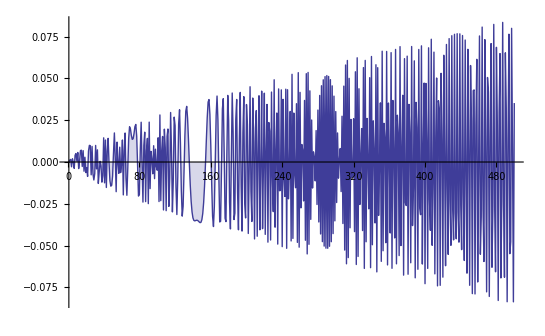

```mathematica
DiscretePlot[fa13a[n,.3,910],{n,1,500}]
```

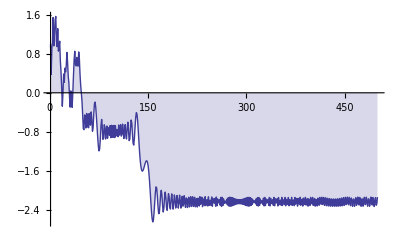

```mathematica
DiscretePlot[ga13a[n,.3,910],{n,1,500}]
```

```mathematica
2HarmonicNumber[n,1-s] HarmonicNumber[n,s]+(n^(1-2 s) s HarmonicNumber[n,1-s]^2)/(-1+s)+(n^(-1+2 s) (-1+s) HarmonicNumber[n,s]^2)/s
```

(n^(1-2 s) s HarmonicNumber[n,1-s]^2)/(-1+s)+2 HarmonicNumber[n,1-s] HarmonicNumber[n,s]+(n^(-1+2 s) (-1+s) HarmonicNumber[n,s]^2)/s

```mathematica
Expand[(n^(s-1/2)(s-1)^(1/2)/s^(1/2)HarmonicNumber[n,s]+n^(1/2-s)s^(1/2)/(s-1)^(1/2)HarmonicNumber[n,1-s])^2]
```

(n^(1-2 s) s HarmonicNumber[n,1-s]^2)/(-1+s)+2 HarmonicNumber[n,1-s] HarmonicNumber[n,s]+n^(-1+2 s) HarmonicNumber[n,s]^2-(n^(-1+2 s) HarmonicNumber[n,s]^2)/s

```mathematica
FullSimplify[((n^(1-2s) s/(1-s)-2^s π^(-1+s) Cos[1/2 π (1-s)] Gamma[1-s]) (n^(-1+2 s)(1-s)/s-2^(1-s) π^-s Cos[(π s)/2] Gamma[s]))^(1/2)]
```

√(2-(2^s n^(-1+2 s) π^(-1+s) Gamma[2-s] Sin[(π s)/2])/s+(n^(1-2 s) (2 π)^-s Csc[(π s)/2] Gamma[1+s] Sin[π s])/(-1+s))

```mathematica
ps60[n_,s_]:=1/(√(2-(2^s n^(-1+2 s) π^(-1+s) Gamma[2-s] Sin[(π s)/2])/s+(n^(1-2 s) (2 π)^-s Csc[(π s)/2] Gamma[1+s] Sin[π s])/(-1+s)))(n^(s-1/2)(s-1)^(1/2)/s^(1/2)HarmonicNumber[n,s]+n^(1/2-s)s^(1/2)/(s-1)^(1/2)HarmonicNumber[n,1-s])
ps60x[n_,s_]:=n^(s-1/2)(s-1)^(1/2)/s^(1/2)HarmonicNumber[n,s]+n^(1/2-s)s^(1/2)/(s-1)^(1/2)HarmonicNumber[n,1-s]
ps61[n_,s_]:=1/(√(2-(2^s n^(-1+2 s) π^(-1+s) Gamma[2-s] Sin[(π s)/2])/s+(n^(1-2 s) (2 π)^-s Csc[(π s)/2] Gamma[1+s] Sin[π s])/(-1+s)))(1/(s^(1/2))/((s-1)^(1/2)))(n^(s-1/2)(s-1)HarmonicNumber[n,s]+n^(1/2-s)s HarmonicNumber[n,1-s])
ps61x[n_,s_]:=n^(s-1/2)(s-1)HarmonicNumber[n,s]+n^(1/2-s)s HarmonicNumber[n,1-s]
ps62[n_,s_]:=1/(√(s(s-1)(2-(2^s n^(-1+2 s) π^(-1+s) Gamma[2-s] Sin[(π s)/2])/s+(n^(1-2 s) (2 π)^-s Csc[(π s)/2] Gamma[1+s] Sin[π s])/(-1+s))))(n^(s-1/2)(1-s)HarmonicNumber[n,s]-n^(1/2-s)s HarmonicNumber[n,1-s])
ps63[n_,s_]:=1/(√(n s(s-1)(2-(2^s n^(-1+2 s) π^(-1+s) Gamma[2-s] Sin[(π s)/2])/s+(n^(1-2 s) (2 π)^-s Csc[(π s)/2] Gamma[1+s] Sin[π s])/(-1+s))))(n^s(1-s)HarmonicNumber[n,s]-n^(1-s)s HarmonicNumber[n,1-s])
ps64[n_,s_]:=1/(√(2s(s-1)n-2^s(s-1) n^(2 s) π^(-1+s) Gamma[2-s] Sin[(π s)/2]+n^(2-2 s) (2 π)^-s s  Csc[(π s)/2] Gamma[1+s] Sin[π s]))(n^s(1-s)HarmonicNumber[n,s]-n^(1-s)s HarmonicNumber[n,1-s])
```

```mathematica
ps64[100000000000000,N@ZetaZero@2+3I+.2]
```

1.11394+0.155879 ⅈ

```mathematica
(Zeta[N@ZetaZero@2+3I+.2]Zeta[1-(N@ZetaZero@2+3I+.2)])^(1/2)
```

1.11394+0.155879 ⅈ

```mathematica
n^(s-1/2)(s-1)HarmonicNumber[n,s]+n^(1/2-s)s HarmonicNumber[n,1-s]
```

n^(1/2-s) s HarmonicNumber[n,1-s]+n^(-1/2+s) (-1+s) HarmonicNumber[n,s]

```mathematica
n^(s-1/2)(s-1)HarmonicNumber[n,s]+n^(1/2-s)s HarmonicNumber[n,1-s]/.s->1/2-x
```

n^-x (-1/2-x) HarmonicNumber[n,1/2-x]+n^x (1/2-x) HarmonicNumber[n,1/2+x]

```mathematica
n^(s-1/2)(s-1)HarmonicNumber[n,s]+n^(1/2-s)s HarmonicNumber[n,1-s]/.s->N@ZetaZero@1/.n->100000000000
```

0.+0.0000446902 ⅈ

```mathematica
(n^(s-a)(1-s)HarmonicNumber[n,s]-n^(1-a-s)s HarmonicNumber[n,1-s])/.s->N@ZetaZero@1/.n->1000/.a->0
```

0.-14.1347 ⅈ

```mathematica
N@ZetaZero@1
```

0.5+14.1347 ⅈ

```mathematica
(n^(s-a)(1-b-s)HarmonicNumber[n,s]-n^(1-a-s)(s+b) HarmonicNumber[n,1-s])/.s->N@ZetaZero@1/.n->1000000/.a->1/2/.b->1/2
```

-2.49999-0.0141347 ⅈ

```mathematica
(n^(s-a)(1-b-s)HarmonicNumber[n,s]-n^(1-a-s)(s+b) HarmonicNumber[n,1-s])/.s->N@ZetaZero@1/.n->100000000/.a->1/2/.b->0
```

0.-0.00141347 ⅈ

```mathematica
ps[n_,s_,a_,b_,c_]:=(n^(s-a)(1-b-s)HarmonicNumber[n,s-c]-n^(1-a-s)(s+b) HarmonicNumber[n,1-c-s])
psa[n_,s_,a_,b_,c_]:=-ps[n,s,a,b,c] n^a
```

```mathematica
N@ps[10000,N@ZetaZero@1,0,0,0]
```

0.-14.1347 ⅈ

```mathematica
(n^s(1-s)HarmonicNumber[n,s]-n^(1-s)s HarmonicNumber[n,1-s])/.s->N@ZetaZero@1/.n->1000
```

0.-14.1347 ⅈ

```mathematica
FullSimplify[√(2s(s-1)n-2^s(s-1) n^(2 s) π^(-1+s) Gamma[2-s] Sin[(π s)/2]+n^(2-2 s) (2 π)^-s s  Csc[(π s)/2] Gamma[1+s] Sin[π s])]
```

√(-2^s n^(2 s) π^(-1+s) (-1+s) Gamma[2-s] Sin[(π s)/2]+n s (-2+2 s+n^(1-2 s) (2 π)^-s Csc[(π s)/2] Gamma[1+s] Sin[π s]))

```mathematica
-2^s n^(2 s) π^(-1+s) (-1+s) Gamma[2-s] Sin[(π s)/2]+n^(2-2 s) (2 π)^-s s/Sin[(π s)/2] Gamma[1+s] Sin[π s]
```

-2^s n^(2 s) π^(-1+s) (-1+s) Gamma[2-s] Sin[(π s)/2]+n^(2-2 s) (2 π)^-s s Csc[(π s)/2] Gamma[1+s] Sin[π s]

```mathematica
pt1[n_,s_]:=(n^s(1-s)HarmonicNumber[n,s]-n^(1-s)s HarmonicNumber[n,1-s])
pt2[n_,s_]:=(n^s(1-s)Sum[j^-s,{j,1,n}]-n^(1-s)s Sum[j^(s-1),{j,1,n}])
pt3[n_,s_]:=Sum[(1-s)(n/j)^s-s (n/j)^(1-s),{j,1,n}]
pt4[n_,s_]:=Sum[(1-(1/2-s))(n/j)^(1/2-s)-(1/2-s) (n/j)^(1-(1/2-s)),{j,1,n}]
pt4a[n_,s_]:=pt4[n,1/2-s]
pt5[n_,s_]:=Sum[1/2 ((n/j)^(1/2-s)-(n/j)^(1/2+s))+s((n/j)^(1/2-s) +(n/j)^(1/2+s)),{j,1,n}]
pt5a[n_,s_]:=pt5[n,1/2-s]
pt6[n_,s_]:=Sum[(n/j)^(1/2)(1/2 ((n/j)^-s-(n/j)^(+s))+s((n/j)^-s +(n/j)^(+s))),{j,1,n}]
pt6a[n_,s_]:=pt6[n,1/2-s]
```

```mathematica
pt6a[1000,N@ZetaZero@1]
```

0.-14.1347 ⅈ

```mathematica
Expand[(1-(1/2-s))(n/j)^(1/2-s)-(1/2-s) (n/j)^(1-(1/2-s))]
```

1/2 (n/j)^(1/2-s)-1/2 (n/j)^(1/2+s)+(n/j)^(1/2-s) s+(n/j)^(1/2+s) s

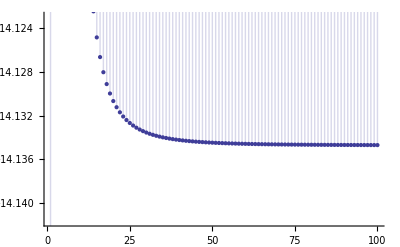

```mathematica
DiscretePlot[Im@ pt5a[n,N@ZetaZero@1],{n,1,100}]
```

```mathematica
pro3[n_,x_]:=  n^(1/2-ⅈ x) (-ⅈ/2+ x) HarmonicNumber[n,1/2-ⅈ x]+ n^(1/2+ⅈ x) (ⅈ/2+ x) HarmonicNumber[n,1/2+ⅈ x]
```

```mathematica
Chop@pro3[1000,N@Im@ZetaZero@20]
```

77.1448

```mathematica
N@Im@ZetaZero@20
```

77.1448

```mathematica
po[n_,s_]:=Sum[ (n/j)^(1/2) (2 s Cos[ s Log[j/n]]+Sin[s Log[j/n]]),{j,1,n}]
po2[n_,s_]:=Sum[ (n/j)^(1/2) (2 s Cos[ s Log[n/j]]-Sin[s Log[n/j]]),{j,1,n}]
```

```mathematica
Chop@po2[1000,N@Im@ZetaZero@20]
```

77.1448

```mathematica
ps14x[n_,s_]:=   HarmonicNumber[n,s]/(1-2^(1-s) n^(1-2s) (s/(1-s)) π^-s Cos[(π s)/2] Gamma[s])-HarmonicNumber[n,1-s]/(n^(2s-1)  (1-s)/s-2^(1-s)  π^-s Cos[(π s)/2] Gamma[s])
ps14y[n_,s_]:=   n^(2s-1)  (1-s)/s HarmonicNumber[n,s]/(n^(2s-1)  (1-s)/s-2^(1-s)  π^-s Cos[(π s)/2] Gamma[s])-HarmonicNumber[n,1-s]/(n^(2s-1)  (1-s)/s-2^(1-s)  π^-s Cos[(π s)/2] Gamma[s])
ps14y2[n_,s_]:=   (n^(2s-1)  (1-s)/s HarmonicNumber[n,s]-HarmonicNumber[n,1-s])/(n^(2s-1)  (1-s)/s-2^(1-s)  π^-s Cos[(π s)/2] Gamma[s])
ps14y3[n_,s_]:=   ((n^(2s-1)  (1-s)/s-1) Re@HarmonicNumber[n,s]+I(n^(2s-1)  (1-s)/s+1)Im@HarmonicNumber[n,s])/(n^(2s-1)  (1-s)/s-2^(1-s)  π^-s Cos[(π s)/2] Gamma[s])
ps14y32[n_,s_]:=   (n^(2s-1)  (1-s)/s-1) Re@HarmonicNumber[n,s]+I(n^(2s-1)  (1-s)/s+1)Im@HarmonicNumber[n,s]
ps14y33[n_,s_]:=   {(n^(2s-1)  (1-s)/s-1), Re@HarmonicNumber[n,s],I(n^(2s-1)  (1-s)/s+1),Im@HarmonicNumber[n,s]}
```

```mathematica
ps14y33[10000000000,N@ZetaZero@1]
```

{-0.228237+0.63591 ⅈ,-6654.71,-0.63591+1.77176 ⅈ,2388.47}

```mathematica
Zeta[.5+17I]
```

1.94665+0.895405 ⅈ

```mathematica
FullSimplify[(n^(2s-1)  (1-s)/s-1) Re@HarmonicNumber[n,s]+I(n^(2s-1)  (1-s)/s+1)Im@HarmonicNumber[n,s]]
```

-Conjugate[HarmonicNumber[n,s]]-(n^(-1+2 s) (-1+s) HarmonicNumber[n,s])/s

```mathematica
-Conjugate[HarmonicNumber[n,s]]-(n^(-1+2 s) (-1+s) HarmonicNumber[n,s])/s/.n->10000000000000/.s->N@ZetaZero@1
```

1.80793×10^-7-2.67493×10^-7 ⅈ

```mathematica
FullSimplify[n^(2s-1)  (1-s)/s-1]
```

-1+n^(-1+2 s) (-1+1/s)

```mathematica
FullSimplify[(n^(2s-1)  (1-s)/s+1)]
```

1+n^(-1+2 s) (-1+1/s)

```mathematica
FullSimplify[(1-s)n^(1-s)/(s-1) ]
```

-n^(1-s)

```mathematica
(n^(1-s-x)/(s+x-1))(s-1+x)n^x
```

n^(1-s)

```mathematica
FullSimplify[Expand[-s(1-s)Integrate[ FractionalPart[t]/t^(s+1),{t,n,Infinity}]+-(s-1+x)n^x(s+x)Integrate[ FractionalPart[t]/t^(s+1+x),{t,n,Infinity}]]]
```

(-1+s) s ∫_n^∞ t^(-1-s) FractionalPart[t]ⅆt-n^x (-1+s+x) (s+x) ∫_n^∞ t^(-1-s-x) FractionalPart[t]ⅆt

```mathematica
Limit[(-1+s) s ∫_n^∞ t^(-1-s) FractionalPart[t]ⅆt-n^x (-1+s+x) (s+x) ∫_n^∞ t^(-1-s-x) FractionalPart[t]ⅆt,n->Infinity]
```

$Aborted

```mathematica
Integrate[(-s)(1-s) FractionalPart[t]/t^(s+1)+(-1)(s-1+x)n^x(s+x) FractionalPart[t]/t^(s+1+x),{t,n,Infinity}]
```

```mathematica
FullSimplify[Expand[(-s)(1-s) FractionalPart[t]/t^(s+1)+(-1)(s-1+x)n^x(s+x) FractionalPart[t]/t^(s+1+x)]]
```

t^(-1-s-x) ((-1+s) s t^x-n^x (-1+s+x) (s+x)) FractionalPart[t]

```mathematica
Integrate[((-s)(1-s) /t^(s+1)+(-1)(s-1+x)n^x(s+x) /t^(s+1+x))FractionalPart[t],{t,n,Infinity}]
```

```mathematica
FullSimplify[((-s)(1-s) /t^(s+1)+(-1)(s-1+x)n^x(s+x) /t^(s+1+x))FractionalPart[t]]
```

t^(-1-s) ((-1+s) s-n^x t^-x (-1+s+x) (s+x)) FractionalPart[t]

```mathematica
Integrate[t^(-1-s) ((-1+s) s-n^x t^-x (-1+s+x) (s+x)) FractionalPart[t],{t,n,Infinity}]
```

∫_n^∞ t^(-1-s) ((-1+s) s-n^x t^-x (-1+s+x) (s+x)) FractionalPart[t]ⅆt

```mathematica
pr[n_,s_,x_]:=∫_n^∞ t^(-1-s) ((-1+s) s-n^x t^-x (-1+s+x) (s+x)) FractionalPart[t]ⅆt
pr2[n_,s_,x_]:=s(s-1)∫_n^∞ ( 1-(n/t)^x (1+x/(s-1)) (1+x/s)) FractionalPart[t]/t^(s+1)ⅆt
```

```mathematica
N@pr2[10000000000000000,.1+I,.1+3I]
```

0.+0. ⅈ

```mathematica
N[10000000000^(-1/2)]
```

0.00001

```mathematica
FullSimplify[Expand[t^(-1-s) ((-1+s) s-n^x t^-x (-1+s+x) (s+x))]]
```

t^(-1-s-x) ((-1+s) s t^x-n^x (-1+s+x) (s+x))

```mathematica
FullSimplify[(s-1+x) (s+x)/(s-1)/s]
```

((-1+s+x) (s+x))/((-1+s) s)

```mathematica
FullSimplify[t^(-1-s)s(s-1) ( 1-(n/t)^x (1+x/(s-1)) (1+x/s))]
```

t^(-1-s) ((-1+s) s-(n/t)^x (-1+s+x) (s+x))

```mathematica
N@pr[10000,.3+I,.3+3I]
```

0.0464083+0.133533 ⅈ

```mathematica
N@pr2[10000,.3+I,.3+3I]
```

0.0464083+0.133533 ⅈ

```mathematica
fl[s2_]:=Limit[(1/2)s(s-1)Pi^(-s/2)Gamma[s/2],s->s2]
```

```mathematica
fl[1-s]
```

-1/2 π^(1/2 (-1+s)) (1-s) s Gamma[(1-s)/2]

```mathematica
so[n_,s_]:=(1-s)(Zeta[s]-HarmonicNumber[n,s])-s n^(1-2s) (Zeta[1-s]-HarmonicNumber[n,1-s])
so2[n_,s_]:=((1/fl[s])(1-s)n^s(fl[s]Zeta[s]-fl[s]HarmonicNumber[n,s])-(1/fl[1-s])s n^(1-s) (fl[1-s]Zeta[1-s]-fl[1-s]HarmonicNumber[n,1-s]))n^(-s)
so2a[n_,s_]:=((1/fl[s])(1-s)n^s(fl[s]Zeta[s]-fl[s]HarmonicNumber[n,s])-(1/fl[1-s])s n^(1-s) (fl[1-s]Zeta[1-s]-fl[1-s]HarmonicNumber[n,1-s]))
so3[n_,s_]:=((1/fl[s])(1-s)n^s(fl[s]Zeta[s]-fl[s]HarmonicNumber[n,s])-(1/fl[1-s])s n^(1-s) (fl[s]Zeta[s]-fl[1-s]HarmonicNumber[n,1-s]))
so4[n_,s_]:=(1-s)n^s/fl[s](fl[s]Zeta[s]-fl[s]HarmonicNumber[n,s])-s n^(1-s)/fl[1-s] (fl[s]Zeta[s]-fl[1-s]HarmonicNumber[n,1-s])
so5[n_,s_]:=(1-s)n^s/fl[s]fl[s]Zeta[s]-s n^(1-s)/fl[1-s] fl[s]Zeta[s]-(1-s)n^s HarmonicNumber[n,s]+s n^(1-s) HarmonicNumber[n,1-s]
so6[n_,s_]:=((1-s)n^s/fl[s]-s n^(1-s)/fl[1-s])( fl[s]Zeta[s])-(1-s)n^s HarmonicNumber[n,s]-s n^(1-s) HarmonicNumber[n,1-s]
so7[n_,s_]:=( fl[s]Zeta[s])-((1-s)n^s HarmonicNumber[n,s]-s n^(1-s) HarmonicNumber[n,1-s])/((1-s)n^s/fl[s]-s n^(1-s)/fl[1-s])
so8[n_,s_]:=((1-s)n^s HarmonicNumber[n,s]-s n^(1-s) HarmonicNumber[n,1-s])/((1-s)n^s/fl[s]-s n^(1-s)/fl[1-s]) 
so9[n_,s_]:=(n^s (1-s) HarmonicNumber[n,s]-n^(1-s) s HarmonicNumber[n,1-s])/((2 n^(1-s) π^((1-s)/2))/((1-s) Gamma[(1-s)/2])-(2 n^s π^(s/2))/(s Gamma[s/2]))
so10[n_,s_]:=(n^s (1-s) HarmonicNumber[n,s]-n^(1-s) s HarmonicNumber[n,1-s])/((2 n^(1-s) π^((1-s)/2))/((1-s) Gamma[1/2-s/2])-(2 n^s π^(s/2))/(s Gamma[s/2]))
so11[n_,s_]:=(n^s (1-s) HarmonicNumber[n,s]-n^(1-s) s HarmonicNumber[n,1-s])/(2 n^(1-s) π^((1-s)/2)(Gamma[-s/2]/(2^(1+s) Pi^(1/2) Gamma[-s](1-s)))-2 n^s π^(s/2) (Gamma[s/2+1/2]/(2^(1-s) Pi^(1/2)Gamma[s]s )))
so12[n_,s_]:=(n^s (1-s) HarmonicNumber[n,s]-n^(1-s) s HarmonicNumber[n,1-s])/(2 n^(1-s) π^((1-s)/2)Gamma[-s/2]/(2^(1+s) Pi^(1/2) Gamma[-s](1-s))-2 n^s π^(s/2) Gamma[s/2+1/2]/(2^(1-s) Pi^(1/2)Gamma[s]s ))
so13[n_,s_]:=(n^s (1-s) HarmonicNumber[n,s]-n^(1-s) s HarmonicNumber[n,1-s])/((n^(1-s) π^(1/2-s/2))/Gamma[3/2-s/2]-(n^s π^(s/2))/Gamma[1+s/2])
so14[n_,s_]:=(n^s (1-s) HarmonicNumber[n,s]-n^(1-s) s HarmonicNumber[n,1-s])/((n^(1-s) π^((1-s)/2))/Gamma[1+(1-s)/2]-(n^s π^(s/2))/Gamma[1+s/2])
zet14[n_,s_]:=so14[n,s]/fl[s]
so15[n_,s_]:=(n^s (1-s) HarmonicNumber[n,s]-n^(1-s) s HarmonicNumber[n,1-s])/((n^(1-s) π^((1-s)/2)Gamma[(s-1)/2])/(Gamma[1-(s-1)/2]Gamma[(s-1)/2])-(n^s π^(s/2)Gamma[-s/2])/(Gamma[1+s/2]Gamma[-s/2]))
so16[n_,s_]:=(n^s (1-s) HarmonicNumber[n,s]-n^(1-s) s HarmonicNumber[n,1-s])/((n^(1-s) π^((1-s)/2)Gamma[(s-1)/2])/(Pi/Sin[ Pi (s-1)/2])-(n^s π^(s/2)Gamma[-s/2])/(Pi/Sin[Pi(1+s/2)]))
so17[n_,s_]:=(n^s (1-s) HarmonicNumber[n,s]-n^(1-s) s HarmonicNumber[n,1-s])/(n^(1-s) π^(-1/2-s/2)Gamma[(s-1)/2]Sin[ Pi (s-1)/2]-n^s π^(s/2-1)Gamma[-s/2]Sin[Pi(1+s/2)])
so18[n_,s_]:=(n^s (1-s) HarmonicNumber[n,s]-n^(1-s) s HarmonicNumber[n,1-s])/(n^s π^(s/2-1)Gamma[-s/2]Sin[(π s)/2]-n^(1-s) π^(-(s+1)/2)Gamma[(s-1)/2]Cos[ (π s)/2])
zet[n_,s_]:=so18[n,s]/fl[s]
```

```mathematica
so18[1000000000000000,-.3+17I]/fl[-.3+17I]
```

2.83973+1.93155 ⅈ

```mathematica
N@zet14[1000000000000000,.53]
```

-1.5857

```mathematica
N@Zeta[.53]
```

-1.5857

```mathematica
((1-s)n^s HarmonicNumber[n,s]-s n^(1-s) HarmonicNumber[n,1-s])/((1-s)n^s/fl[s]-s n^(1-s)/fl[1-s])
```

(-n^(1-s) s HarmonicNumber[n,1-s]+n^s (1-s) HarmonicNumber[n,s])/((2 n^(1-s) π^((1-s)/2))/((1-s) Gamma[(1-s)/2])+(2 n^s π^(s/2) (1-s))/((-1+s) s Gamma[s/2]))

```mathematica
FullSimplify[(2 n^(1-s) π^((1-s)/2))/((1-s) Gamma[(1-s)/2])-(2 n^s π^(s/2))/(s Gamma[s/2])/.s->3]
```

-(4 n^3 π)/3

```mathematica
Gamma[s/2]/.s->5
```

(3 √π)/4

```mathematica
Gamma[s/2]/.s->5
```

```mathematica
(-n^(1-s) s HarmonicNumber[n,1-s]+n^s (1-s) HarmonicNumber[n,s])/((2 n^(1-s) π^((1-s)/2))/((1-s) Gamma[(1-s)/2])-(2 n^s π^(s/2))/(s Gamma[s/2]))/.s->1-s
```

(n^(1-s) s HarmonicNumber[n,1-s]-n^s (1-s) HarmonicNumber[n,s])/(-(2 n^(1-s) π^((1-s)/2))/((1-s) Gamma[(1-s)/2])+(2 n^s π^(s/2))/(s Gamma[s/2]))

```mathematica
FullSimplify[2 n^(1-s) π^((1-s)/2)Gamma[-s/2]/(2^(1+s) Pi^(1/2) Gamma[-s](1-s))]
```

(n^(1-s) π^(1/2-s/2))/Gamma[3/2-s/2]

```mathematica
FullSimplify[2 n^s π^(s/2) Gamma[s/2+1/2]/(2^(1-s) Pi^(1/2)Gamma[s]s )]
```

(n^s π^(s/2))/Gamma[1+s/2]

```mathematica
n^s (1-s) HarmonicNumber[n,s]-n^(1-s) s HarmonicNumber[n,1-s]/.n->10000000/.s->N@ZetaZero@1
```

0.-14.1347 ⅈ

```mathematica
Gamma[(s-1)/2]/.s->.3
```

-3.95656

```mathematica
2Gamma[(s-1)/2+1]/ (s-1)/.s->.3
```

-3.95656

```mathematica
Gamma[2]
```

1

```mathematica
(n^(1-s) π^((1-s)/2))/Gamma[1-(s-1)/2]-(n^s π^(s/2))/Gamma[1+s/2]/.s->1/2
```

0

```mathematica
N@Limit[(1/2)s(s-1)Pi^(-s/2)Gamma[s/2],s->1/2]
```

-0.340411

```mathematica
Gamma[1]
```

1

```mathematica
fl[s2_]:=Limit[(1/2)s(s-1)Pi^(-s/2)Gamma[s/2],s->s2]
```

```mathematica
n^s (1-s) HarmonicNumber[n,s]-n^(1-s) s HarmonicNumber[n,1-s]/.s->1/2
```

0

```mathematica
so10[n_,s_]:=(n^s (1-s) HarmonicNumber[n,s]-n^(1-s) s HarmonicNumber[n,1-s])/((2 n^(1-s) π^((1-s)/2))/((1-s) Gamma[1/2-s/2])-(2 n^s π^(s/2))/(s Gamma[s/2]))
zet10[n_,s_]:=so10[n,s]/fl[s]
so10a[n_,s_]:=HarmonicNumber[n,s]/((2 n^(1-2s) π^((1-s)/2))/((1-s)(1-s) Gamma[(1-s)/2])-(2  π^(s/2))/(s (1-s)Gamma[s/2]))-HarmonicNumber[n,1-s]/((2  π^((1-s)/2))/((1-s) s Gamma[(1-s)/2])-(2 n^(2s-1) π^(s/2))/(s s Gamma[s/2]))
so10b[n_,s_]:=((1-s)HarmonicNumber[n,s])/((n^(1-2s) π^((1-s)/2))/Gamma[1+(1-s)/2]-π^(s/2)/Gamma[1+s/2])-(s HarmonicNumber[n,1-s])/(π^((1-s)/2)/Gamma[1+(1-s)/2]-(n^(2s-1) π^(s/2))/Gamma[1+s/2])
zet10b[n_,s_]:=so10b[n,s]/fl[s]
sosub[n_,s_]:=((1-s)HarmonicNumber[n,s])/((n^(1-2s) π^((1-s)/2))/Gamma[1+(1-s)/2]-π^(s/2)/Gamma[1+s/2])
so10c[n_,s_]:=sosub[n,s]+sosub[n,1-s]
zet10c[n_,s_]:=so10c[n,s]/fl[s]
sosub2[n_,s_]:=((1-s)n^s HarmonicNumber[n,s]Gamma[1+(1-s)/2]Gamma[1+s/2])/(n^(1-s) π^((1-s)/2)Gamma[1+s/2]- n^s π^(s/2) Gamma[1+(1-s)/2])
so10c2[n_,s_]:=sosub2[n,s]+sosub2[n,1-s]
zet10c2[n_,s_]:=so10c2[n,s]/fl[s]
sosub3[n_,s_]:=((1-s)HarmonicNumber[n,s])/(π^(s/2-1) Gamma[-s/2]Sin[Pi s/2]-n^(1-2s) π^((-s-1)/2)Gamma[(s-1)/2]Cos[Pi s/2])
so10c3[n_,s_]:=sosub3[n,s]+sosub3[n,1-s]
zet10c3[n_,s_]:=so10c3[n,s]/fl[s]
sosub4[n_,s_]:=((1-s)HarmonicNumber[n,s])/((n^(1-2s) π^((1-s)/2))/Gamma[1/2 + 1+-s/2]-π^(s/2)/Gamma[1+s/2])
so10c4[n_,s_]:=sosub4[n,s]+sosub4[n,1-s]
zet10c4[n_,s_]:=so10c4[n,s]/fl[s]
```

```mathematica
so10c4[10000,N@ZetaZero@1]
```

-8.7111×10^-6+0. ⅈ

```mathematica
zet10c4[10000000,.6]
```

-1.95268

```mathematica
Zeta[.6]
```

-1.95266

```mathematica
so10[10000,1.15+3I]
```

0.40559+0.0371621 ⅈ

```mathematica
FullSimplify[(2 n^(1-2s) π^((1-s)/2))/((1-s)(1-s) Gamma[(1-s)/2])-(2  π^(s/2))/(s (1-s)Gamma[s/2])]
```

(π^(-s/2) (-(n^(1-2 s) √π)/Gamma[3/2-s/2]+π^s/Gamma[1+s/2]))/(-1+s)

```mathematica
FullSimplify[(2  π^((1-s)/2))/((1-s) s Gamma[(1-s)/2])-(2 n^(2s-1) π^(s/2))/(s s Gamma[s/2])]
```

(π^(-s/2) ((√π)/Gamma[3/2-s/2]-(n^(-1+2 s) π^s)/Gamma[1+s/2]))/s

```mathematica
((1-s)HarmonicNumber[n,s])/((n^(1-2s) π^((1-s)/2))/Gamma[1+(1-s)/2]-π^(s/2)/Gamma[1+s/2])/.s->1-s
```

(s HarmonicNumber[n,1-s])/(-π^((1-s)/2)/Gamma[1+(1-s)/2]+(n^(1-2 (1-s)) π^(s/2))/Gamma[1+s/2])

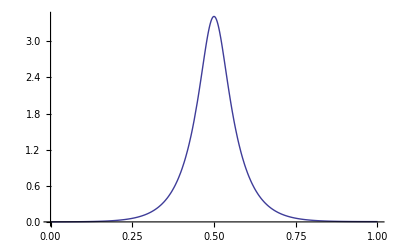

```mathematica
Plot[{Im@sosub[100000000,x+12I]},{x,0,1}]
```

```mathematica
fla[s2_]:=Limit[(1/2)s(s-1)Pi^(-s/2)Gamma[s/2],s->s2]
so10x[n_,s_]:=(n^s (1-s) HarmonicNumber[n,s]-n^(1-s) s HarmonicNumber[n,1-s])/((2 n^(1-s) π^((1-s)/2))/((1-s) Gamma[1/2-s/2])-(2 n^s π^(s/2))/(s Gamma[s/2]))
so10x2[n_,s_]:=((n^s (1-s) HarmonicNumber[n,s]-n^(1-s) s HarmonicNumber[n,1-s])s(1-s)Gamma[1/2-s/2]Gamma[s/2])/(2 n^(1-s) π^((1-s)/2)s Gamma[s/2]-2 n^s π^(s/2) (1-s)Gamma[1/2-s/2])
so10x3[n_,s_]:=((n^s (1-s) HarmonicNumber[n,s]-n^(1-s) s HarmonicNumber[n,1-s])s(1-s)Gamma[1/2-s/2]Gamma[s/2])/(2 n^(1-s) π^((1-s)/2)s Gamma[s/2]-2 n^s π^(s/2) (1-s)Gamma[1/2-s/2])
so14x[n_,s_]:=(n^s (1-s) HarmonicNumber[n,s]-n^(1-s) s HarmonicNumber[n,1-s])/((n^(1-s) π^((1-s)/2))/Gamma[1+(1-s)/2]-(n^s π^(s/2))/Gamma[1+s/2])
so14x2[n_,s_]:=((n^s (1-s) HarmonicNumber[n,s]-n^(1-s) s HarmonicNumber[n,1-s])Gamma[1+(1-s)/2]Gamma[1+s/2])/(n^(1-s) π^((1-s)/2)Gamma[1+s/2]-n^s π^(s/2)Gamma[1+(1-s)/2])
zet10x[n_,s_]:=so10x3[n,s]/fla[s]
zet14x[n_,s_]:=so14x2[n,s]/fla[s]
so14y[n_,s_]:=(n^s (1-s) HarmonicNumber[n,s])/((n^(1-s) π^((1-s)/2))/Gamma[1+(1-s)/2]-(n^s π^(s/2))/Gamma[1+s/2])-(n^(1-s) s HarmonicNumber[n,1-s])/((n^(1-s) π^((1-s)/2))/Gamma[1+(1-s)/2]-(n^s π^(s/2))/Gamma[1+s/2])
so14y2[n_,s_]:=1/((n^(1-2s) π^((1-s)/2))/(Gamma[1+(1-s)/2](1-s))-π^(s/2)/(Gamma[1+s/2](1-s)))HarmonicNumber[n,s]-1/(π^((1-s)/2)/(Gamma[1+(1-s)/2]s)-(n^(2s-1) π^(s/2))/(Gamma[1+s/2]s))HarmonicNumber[n,1-s]
so14y3[n_,s_]:=1/((Gamma[1+s/2] n^(1-2s) π^((1-s)/2)-Gamma[1+(1-s)/2] π^(s/2))/(Gamma[1+s/2]Gamma[1+(1-s)/2](1-s)))HarmonicNumber[n,s]-1/((Gamma[1+s/2] π^((1-s)/2)-Gamma[1+(1-s)/2] n^(2s-1) π^(s/2))/(Gamma[1+s/2]Gamma[1+(1-s)/2]s))HarmonicNumber[n,1-s]
so14y4[n_,s_]:=(Gamma[1+s/2]Gamma[1+(1-s)/2](1-s))/(Gamma[1+s/2] n^(1-2s) π^((1-s)/2)-Gamma[1+(1-s)/2] π^(s/2))HarmonicNumber[n,s]-(Gamma[1+s/2]Gamma[1+(1-s)/2]s)/(Gamma[1+s/2] π^((1-s)/2)-Gamma[1+(1-s)/2] n^(2s-1) π^(s/2))HarmonicNumber[n,1-s]
so14y5[n_,s_]:=(Gamma[1+s/2]Gamma[1+(1-s)/2])/(Gamma[1+s/2] n^(1-s) π^((1-s)/2)-Gamma[1+(1-s)/2] π^(s/2)n^s)(1-s)n^sHarmonicNumber[n,s]-(Gamma[1+s/2]Gamma[1+(1-s)/2])/(Gamma[1+s/2]n^(1-s) π^((1-s)/2)-Gamma[1+(1-s)/2] n^s π^(s/2))s n^(1-s)HarmonicNumber[n,1-s]
so14y6[n_,s_]:=(Gamma[1+s/2]Gamma[1+(1-s)/2])/(Gamma[1+s/2] n^(1-s) π^((1-s)/2)-Gamma[1+(1-s)/2] π^(s/2)n^s)((1-s)n^s HarmonicNumber[n,s]-s n^(1-s)HarmonicNumber[n,1-s])
zet14y[n_,s_]:=so14y6[n,s]/fla[s]
```

```mathematica
zet14y[100000,.3+6I]
```

0.818794+0.373409 ⅈ

```mathematica
Zeta[.3+6I]
```

0.81858+0.373183 ⅈ

```mathematica
so14x2[100000,0]
```

100000/199999

```mathematica
FullSimplify[Gamma[1+(1-s)/2]Gamma[1+s/2]]
```

Gamma[3/2-s/2] Gamma[1+s/2]

```mathematica
sosub2[n_,s_]:=((1-s)n^s HarmonicNumber[n,s])/((n^(1-s) π^((1-s)/2))/Gamma[1+(1-s)/2]-(n^s π^(s/2))/Gamma[1+s/2])
sosub2a[n_,s_]:=(1-s)n^s HarmonicNumber[n,s]
sosub2b[n_,s_]:=(n^(1-s) π^((1-s)/2))/Gamma[1+(1-s)/2]-(n^s π^(s/2))/Gamma[1+s/2]
sosub2x[n_,s_]:=((1-s) HarmonicNumber[n,s])/((n^(1-2 s) π^((1-s)/2))/Gamma[1+(1-s)/2]-π^(s/2)/Gamma[1+s/2])
```

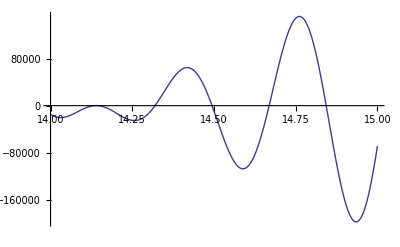

```mathematica
Plot[Im@(sosub2a[100000000,.5+x I]-sosub2a[100000000,1-(.5+x I)]),{x,14,15}]
```

```mathematica
sosub2x[10000000,N@ZetaZero[100]+.2I]+sosub2x[10000000,1-(N@ZetaZero[100])+.2I]
```

-7.8426×10^-78-3.21638×10^-76 ⅈ

```mathematica
N@ZetaZero[20]
```

0.5+77.1448 ⅈ

```mathematica
(n^(1-2 s) π^((1-s)/2))/Gamma[1+(1-s)/2]/.n->1000000/.s->N@ZetaZero@100
```

-7.01842×10^78-5.52083×10^77 ⅈ

```mathematica
Gamma[1+(1-s)/2](1-s)/.s->.3
```

0.623806

```mathematica
Gamma[(1-s)/2]((1-s)/2)(1-s)/.s->.3
```

0.623806

```mathematica
FullSimplify[Gamma[(1-s)/2]((1-s)/2)(1-s)]
```

(1-s) Gamma[3/2-s/2]

```mathematica
al[s_]:=-1/((1/2)s(1-s)Pi^(-s/2)Gamma[s/2])
al2[s_]:=-1/((1/2)s(1-s)Pi^(-s/2)Gamma[s/2])
al3[s_]:=-1/((1/2)(1-s)Pi^(-s/2)Gamma[s/2])
al4[s_]:=-1/((1/2)Pi^(-s/2)Gamma[s/2])
ssosub[n_,s_]:=((1-s)n^s)/(1/(1/2 (1-s)π^(-(1-s)/2) Gamma[(1-s)/2])n^(1-s)-1/(1/2 s π^(-s/2) Gamma[s/2])n^s)HarmonicNumber[n,s]
ssosub2[n_,s_]:=((1-s)n^s)/((1-s)al[s]n^s-s al[1-s]n^(1-s))HarmonicNumber[n,s]
sso10c[n_,s_]:=ssosub2[n,s]+ssosub2[n,1-s]
szet10c[n_,s_]:=al[s] sso10c[n,s]
ssosub3[n_,s_]:=(s^-1 n^s)/(al4[s]s^-1 n^s-al4[1-s](1-s)^-1 n^(1-s))HarmonicNumber[n,s]
sso10cc[n_,s_]:=ssosub3[n,s]+ssosub3[n,1-s]
szet10cc[n_,s_]:=al4[s] sso10cc[n,s]
```

```mathematica
szet10cc[10000000,.3+4I]
```

0.575751+0.10774 ⅈ

```mathematica
Zeta[.3+4I]
```

0.575756+0.10773 ⅈ

```mathematica
(*
ssosub3[n_,s_]:=((1-s)n^s)/((1-s)al2[s]n^s-s al2[1-s]n^(1-s))HarmonicNumber[n,s]
sso10cc[n_,s_]:=ssosub3[n,s]+ssosub3[n,1-s]
szet10cc[n_,s_]:=al2[s] sso10cc[n,s]

ssosub3[n_,s_]:=((1-s)n^s)/(al4[s]/s n^s-al4[1-s]/(1-s) n^(1-s))HarmonicNumber[n,s]
sso10cc[n_,s_]:=ssosub3[n,s]/s/(1-s)+ssosub3[n,1-s]/s/(1-s)
szet10cc[n_,s_]:=al4[s] sso10cc[n,s] 

*)
```

```mathematica
FullSimplify[Pi^(-(s/2))/Pi^(-(1-s)/2)]
```

π^(1/2-s)

```mathematica
FullSimplify[Gamma[s/2]/Gamma[(1-s)/2]]/.s->2
```

-1/(2 √π)